```mathematica
treeKeys4=Select[Keys[stubbornForm4],With[{g=stubbornForm4[#,"graph"]},TreeGraphQ[g]]&]
```

{31,37,39,49,85,91,93,97,111,117,122,145,193,247,253,255,257,271,279,286,309,325,327,346,351,353,357,369,377,382,400,417,442,448,473,517,577,606,608,637,697,728}

```mathematica
set4=Table[Symbol["m"<>ToString[k]]==stubbornForm4[k,"colofour"],{k,treeKeys4}]
```

{m31==v123x4+v12x3x4+v13x2x4+v1x23x4+v1x2x3x4,m37==v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x3x4,m39==v12x34+v12x3x4+v13x2x4+v1x2x34+v1x2x3x4,m49==v123x4+v1x23x4,m85==v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4,m91==v124x3+v12x3x4+v14x2x3+v1x24x3+v1x2x3x4,m93==v12x34+v12x3x4+v14x2x3+v1x2x34+v1x2x3x4,m97==v124x3+v1x24x3,m111==v12x34+v12x3x4+v1x23x4+v1x2x34+v1x2x3x4,m117==v12x34+v12x3x4+v1x24x3+v1x2x34+v1x2x3x4,m122==v12x34+v1x2x34,m145==v124x3+v14x2x3,m193==v123x4+v13x2x4,m247==v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4,m253==v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4,m255==v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4,m257==v134x2+v1x2x34,m271==v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4,m279==v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4,m286==v13x24+v1x24x3,m309==v134x2+v14x2x3,m325==v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4,m327==v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4,m346==v14x23+v1x23x4,m351==v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4,m353==v1x234+v1x2x34,m357==v1x234+v1x24x3,m369==v1x234+v1x23x4,m377==v1x234,m382==v14x23+v14x2x3,m400==v14x23,m417==v134x2+v13x2x4,m442==v13x24+v13x2x4,m448==v13x24,m473==v134x2,m517==v123x4+v12x3x4,m577==v124x3+v12x3x4,m606==v12x34+v12x3x4,m608==v12x34,m637==v124x3,m697==v123x4,m728==v1234}

```mathematica
graph
```

```mathematica
allGraphVariables4
```

{x0,x1,x2,x3,x4,x6,x9,x10,x12,x13,x14,x16,x18,x22,x26,x27,x28,x30,x31,x36,x37,x39,x40,x45,x49,x54,x63,x72,x81,x82,x84,x85,x87,x90,x91,x93,x94,x97,x108,x109,x110,x111,x112,x117,x118,x120,x121,x122,x136,x145,x162,x165,x168,x190,x193,x218,x243,x244,x245,x246,x247,x252,x253,x255,x256,x257,x270,x271,x273,x274,x276,x279,x280,x282,x283,x286,x300,x309,x324,x325,x327,x328,x333,x334,x336,x337,x342,x346,x351,x352,x353,x354,x355,x357,x360,x361,x363,x364,x365,x367,x369,x373,x377,x382,x391,x400,x414,x417,x442,x445,x448,x473,x486,x487,x488,x516,x517,x546,x576,x577,x606,x607,x608,x637,x666,x697,x728}

```mathematica
ListofVars[v1234==m728&&v123x4==m697&&v124x3==m637&&v12x34==m608&&v12x3x4==m606-m608&&v134x2==m473&&v13x24==m448&&v13x2x4==m442-m448&&v14x23==-m49+m697+m85-m91+m97&&v14x2x3==-m39+m442-m448+m93&&v1x234==m377&&v1x23x4==m49-m697&&v1x24x3==-m637+m97&&v1x2x34==-m608-m91+m93+m97&&v1x2x3x4==m39-m442+m448-m606+m608+m91-m93-m97]//DeleteDuplicates//Sort
```

{m377,m39,m442,m448,m473,m49,m606,m608,m637,m697,m728,m85,m91,m93,m97,v1234,v123x4,v124x3,v12x34,v12x3x4,v134x2,v13x24,v13x2x4,v14x23,v14x2x3,v1x234,v1x23x4,v1x24x3,v1x2x34,v1x2x3x4}

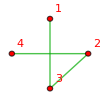
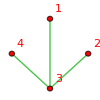
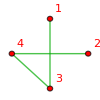
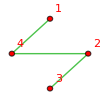
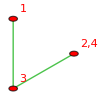
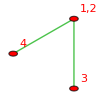
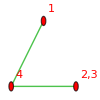
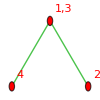
{-Graphics-{93→v12x34+v12x3x4+v14x2x3+v1x2x34+v1x2x3x4,9/2},-Graphics-{91→v124x3+v12x3x4+v14x2x3+v1x24x3+v1x2x3x4,9/2},-Graphics-{85→v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4,9/2},-Graphics-{39→v12x34+v12x3x4+v13x2x4+v1x2x34+v1x2x3x4,9/2},-Graphics-{97→v124x3+v1x24x3,3/2},-Graphics-{606→v12x34+v12x3x4,3/2},-Graphics-{49→v123x4+v1x23x4,3/2},-Graphics-{442→v13x24+v13x2x4,3/2},-Graphics-{697→v123x4,1/2},-Graphics-{637→v124x3,1/2},-Graphics-{608→v12x34,1/2},-Graphics-{473→v134x2,1/2},-Graphics-{448→v13x24,1/2},-Graphics-{377→v1x234,1/2},-Graphics-{728→v1234,1/6}}

```mathematica
Table[CosyPrint4[k],{k,Sort[{377,39,442,448,473,49,606,608,637,697,728,85,91,93,97},VertexCount[stubbornForm4[#1,"graph"]]>VertexCount[stubbornForm4[#2,"graph"]]&]}]
```

```mathematica
Reduce[Fold[And,set4],baseGraphAxioma4Vars]
```

m577==m606-m608+m637&&m517==m606-m608+m697&&m417==m442-m448+m473&&m400==-m49+m697+m85-m91+m97&&m382==-m39+m442-m448-m49+m697+m85-m91+m93+m97&&m37==m39+m448-m637+m91-m93&&m369==m377+m49-m697&&m357==m377-m637+m97&&m353==m377-m608-m91+m93+m97&&m351==m377+m39-m442+m448+m49-m606-m637-m697+m97&&m346==m85-m91+m97&&m327==-m606+m85-m91+m93+m97&&m325==-m606+m608-m637+m85+m97&&m31==m39+m49+m91-m93-m97&&m309==-m39+m442-m448+m473+m93&&m286==m448-m637+m97&&m279==m39+m448-m606-m637+m97&&m271==m39+m448+m49-m606+m608-m637-m697+m91-m93&&m257==m473-m608-m91+m93+m97&&m255==m442-m448+m473-m606+m93&&m253==m442-m606+m608-m637+m91&&m247==m442-m448-m606+m608+m85&&m193==m442-m448+m697&&m145==-m39+m442-m448+m637+m93&&m122==-m91+m93+m97&&m117==m39-m442+m448-m637+m97&&m111==m39-m442+m448+m49-m697&&v1234==m728&&v123x4==m697&&v124x3==m637&&v12x34==m608&&v12x3x4==m606-m608&&v134x2==m473&&v13x24==m448&&v13x2x4==m442-m448&&v14x23==-m49+m697+m85-m91+m97&&v14x2x3==-m39+m442-m448+m93&&v1x234==m377&&v1x23x4==m49-m697&&v1x24x3==-m637+m97&&v1x2x34==-m608-m91+m93+m97&&v1x2x3x4==m39-m442+m448-m606+m608+m91-m93-m97

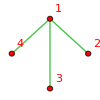
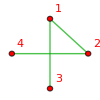
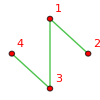
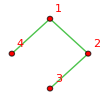
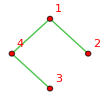
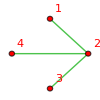
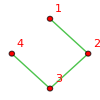
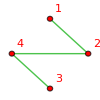
{-Graphics-{351→v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4,9/2},-Graphics-{327→v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4,9/2},-Graphics-{325→v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4,9/2},-Graphics-{279→v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4,9/2},-Graphics-{271→v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4,9/2},-Graphics-{255→v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4,9/2},-Graphics-{253→v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4,9/2},-Graphics-{247→v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4,9/2},-Graphics-{117→v12x34+v12x3x4+v1x24x3+v1x2x34+v1x2x3x4,9/2},-Graphics-{111→v12x34+v12x3x4+v1x23x4+v1x2x34+v1x2x3x4,9/2},-Graphics-{93→v12x34+v12x3x4+v14x2x3+v1x2x34+v1x2x3x4,9/2},-Graphics-{91→v124x3+v12x3x4+v14x2x3+v1x24x3+v1x2x3x4,9/2},-Graphics-{85→v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4,9/2},-Graphics-{39→v12x34+v12x3x4+v13x2x4+v1x2x34+v1x2x3x4,9/2},-Graphics-{37→v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x3x4,9/2},-Graphics-{31→v123x4+v12x3x4+v13x2x4+v1x23x4+v1x2x3x4,9/2},-Graphics-{606→v12x34+v12x3x4,3/2},-Graphics-{577→v124x3+v12x3x4,3/2},-Graphics-{517→v123x4+v12x3x4,3/2},-Graphics-{442→v13x24+v13x2x4,3/2},-Graphics-{417→v134x2+v13x2x4,3/2},-Graphics-{382→v14x23+v14x2x3,3/2},-Graphics-{369→v1x234+v1x23x4,3/2},-Graphics-{357→v1x234+v1x24x3,3/2},-Graphics-{353→v1x234+v1x2x34,3/2},-Graphics-{346→v14x23+v1x23x4,3/2},-Graphics-{309→v134x2+v14x2x3,3/2},-Graphics-{286→v13x24+v1x24x3,3/2},-Graphics-{257→v134x2+v1x2x34,3/2},-Graphics-{193→v123x4+v13x2x4,3/2},-Graphics-{145→v124x3+v14x2x3,3/2},-Graphics-{122→v12x34+v1x2x34,3/2},-Graphics-{97→v124x3+v1x24x3,3/2},-Graphics-{49→v123x4+v1x23x4,3/2},-Graphics-{697→v123x4,1/2},-Graphics-{637→v124x3,1/2},-Graphics-{608→v12x34,1/2},-Graphics-{473→v134x2,1/2},-Graphics-{448→v13x24,1/2},-Graphics-{400→v14x23,1/2},-Graphics-{377→v1x234,1/2},-Graphics-{728→v1234,1/6}}

```mathematica
Table[CosyPrint4[k],{k,Sort[treeKeys4,VertexCount[stubbornForm4[#1,"graph"]]>VertexCount[stubbornForm4[#2,"graph"]]&]}]
```

```mathematica
Length[treeKeys4]
```

42

```mathematica
Flatten[Table[ListofVars[stubbornForm4[ k,"colofour"]],{k,treeKeys4}]]//DeleteDuplicates//Length
```

15

```mathematica
treeKeys3=Select[Keys[stubbornForm3],With[{g=stubbornForm3[#,"graph"]},TreeGraphQ[g]
]&];Length[treeKeys3]
```

7

```mathematica
baseGraphAxioma3//Length
```

5

```mathematica
Flatten[Table[ListofVars[stubbornForm3[ k,"colofour"]],{k,treeKeys3}]]//DeleteDuplicates//Length
```

5

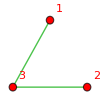
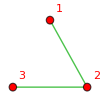
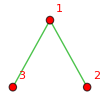
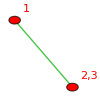
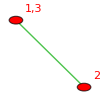
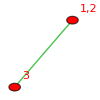
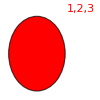
{-Graphics-{4→v12x3+v1x2x3,3/2},-Graphics-{10→v13x2+v1x2x3,3/2},-Graphics-{12→v1x23+v1x2x3,3/2},-Graphics-{14→v1x23,1/2},-Graphics-{16→v13x2,1/2},-Graphics-{22→v12x3,1/2},-Graphics-{26→v123,1/6}}

```mathematica
Table[CosyPrint3[k],{k,treeKeys3}]
```

```mathematica
Reduce[m1==v12x3+v1x2x3&&m2==v13x2+v1x2x3&&m3==v1x23+v1x2x3&&m4==v1x23&&m5==v13x2&&m6==v12x3&&m7==v123,{v12x3,v1x2x3,v13x2,v1x23,v123}]
```

m2==m3-m4+m5&&m1==m3-m4+m6&&v12x3==m6&&v1x2x3==m3-m4&&v13x2==m5&&v1x23==m4&&v123==m7

```mathematica
LinguisticAssistant
```

```mathematica
Reduce[m1==v12x3+v1x2x3&&m2==v13x2+v1x2x3&&m5==v13x2&&m6==v12x3&&m7==v123,{v12x3,v1x2x3,v13x2,v1x23,v123}]
```

m1==m2-m5+m6&&v12x3==m6&&v1x2x3==m2-m5&&v13x2==m5&&v123==m7

```mathematica
treeKeys5=Select[Keys[stubbornForm5],With[{g=stubbornForm5[#,"graph"]},TreeGraphQ[g]
]&]
```

{760,766,768,778,814,820,822,840,846,922,976,982,984,1000,1008,1054,1056,1075,1080,1098,1146,1171,1246,1306,1335,1426,2218,2224,2226,2272,2278,2280,2284,2298,2304,2332,2434,2440,2442,2458,2466,2473,2496,2512,2514,2538,2544,2569,2704,2764,2793,2824,2946,2952,3000,3006,3038,3162,3168,3173,3186,3240,3269,3432,3492,3524,3736,3898,3970,4222,5134,5350,5374,5620,6592,6598,6600,6646,6652,6654,6672,6678,6683,6706,6754,6808,6814,6816,6818,6832,6840,6870,6886,6888,6912,6914,6943,6978,7003,7034,7318,7326,7372,7380,7387,7398,7480,7534,7542,7576,7614,7647,7704,7738,8112,8274,8346,8436,8776,8778,8797,8830,8832,8856,8884,8992,8994,9018,9048,9094,9117,9148,9504,9522,9558,9564,9587,9720,9722,9753,9819,9854,10291,10453,10552,10974,11190,11214,11244,11701,11917,11950,12650,13882,13936,13962,14044,15346,15400,15426,15454,16077,16131,16160,16864,18274,19714,19720,19722,19732,19768,19774,19776,19780,19794,19800,19805,19930,19936,19938,19940,19954,19962,19969,20008,20010,20029,20034,20036,20040,20052,20060,20416,20422,20424,20434,20496,20502,20557,20656,20664,20721,20736,20754,20794,20812,21258,21420,21492,21510,21874,21880,21882,21886,21900,21906,22063,22114,22116,22140,22146,22287,22312,22318,22602,22608,22613,22662,22764,22842,22844,22899,23013,23072,23365,23599,23770,24168,24384,24408,24414,24871,25111,25168,25868,26248,26254,26256,26258,26272,26280,26326,26328,26352,26354,26761,26821,26850,26852,26974,26982,26989,27036,27054,27060,27109,27460,27549,27610,27741,27813,28308,28432,28434,28453,28458,28476,28596,28621,28918,28947,29128,29160,29162,29166,29178,29186,29214,29232,29322,29328,29378,29646,29648,29706,29826,29888,29920,29938,30082,30406,30586,30711,30735,31224,31438,31444,31492,31924,31984,32198,32684,33076,33130,33156,33158,33781,33861,33916,34620,35245,35271,35434,35976,35978,36030,36138,36194,36736,36898,37548,38254,38308,39014,40126,40132,40134,40144,41638,41644,41646,41650,42393,42399,42404,43156,44662,46174,46180,46182,46184,46927,46935,46942,47694,48439,48441,48460,49194,49196,49200,49212,49220,49954,49972,50718,51472,51478,52232,53734,55252,56010,56012,56770,58288,59048}

```mathematica
Flatten[Table[ListofVars[stubbornForm5[ k,"colofour"]],{k,treeKeys5}]]//DeleteDuplicates//Length
```

52

```mathematica
set5=Table[Symbol["m"<>ToString[k]]==stubbornForm5[k,"colofour"],{k,treeKeys5}]
```

{m760==v1234x5+v123x4x5+v124x3x5+v12x34x5+v12x3x4x5+v134x2x5+v13x24x5+v13x2x4x5+v14x23x5+v14x2x3x5+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5,m766==v123x4x5+v124x35+v124x3x5+v12x35x4+v12x3x4x5+v13x24x5+v13x2x4x5+v14x23x5+v14x2x35+v14x2x3x5+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,m768==v123x45+v123x4x5+v124x3x5+v12x3x45+v12x3x4x5+v13x24x5+v13x2x45+v13x2x4x5+v14x23x5+v14x2x3x5+v1x23x45+v1x23x4x5+v1x24x3x5+v1x2x3x45+v1x2x3x4x5,m778==v1234x5+v12x34x5+v134x2x5+v1x234x5+v1x2x34x5,m814==v123x4x5+v12x34x5+v12x3x4x5+v134x25+v134x2x5+v13x25x4+v13x2x4x5+v14x23x5+v14x25x3+v14x2x3x5+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,m820==v123x4x5+v12x35x4+v12x3x4x5+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,m822==v123x45+v123x4x5+v12x3x45+v12x3x4x5+v13x25x4+v13x2x45+v13x2x4x5+v14x23x5+v14x25x3+v14x2x3x5+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,m840==v123x45+v123x4x5+v12x34x5+v12x3x45+v12x3x4x5+v134x2x5+v13x2x45+v13x2x4x5+v14x23x5+v14x2x3x5+v1x23x45+v1x23x4x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m846==v123x45+v123x4x5+v12x35x4+v12x3x45+v12x3x4x5+v13x2x45+v13x2x4x5+v14x23x5+v14x2x35+v14x2x3x5+v1x23x45+v1x23x4x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m922==v1234x5+v124x3x5+v13x24x5+v1x234x5+v1x24x3x5,m976==v124x3x5+v12x34x5+v12x3x4x5+v134x25+v134x2x5+v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,m982==v124x35+v124x3x5+v12x35x4+v12x3x4x5+v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,m984==v124x3x5+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x25x3+v14x2x3x5+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,m1000==v124x35+v124x3x5+v12x34x5+v12x35x4+v12x3x4x5+v134x2x5+v13x24x5+v13x2x4x5+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m1008==v124x35+v124x3x5+v12x35x4+v12x3x45+v12x3x4x5+v13x24x5+v13x2x45+v13x2x4x5+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m1054==v12x34x5+v12x35x4+v12x3x4x5+v134x25+v134x2x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m1056==v12x34x5+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x25x4+v13x2x45+v13x2x4x5+v14x25x3+v14x2x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m1075==v12x34x5+v134x25+v134x2x5+v1x25x34+v1x2x34x5,m1080==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v134x2x5+v13x2x45+v13x2x4x5+v14x2x35+v14x2x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m1098==v12x345+v12x34x5+v134x2x5+v1x2x345+v1x2x34x5,m1146==v124x3x5+v13x245+v13x24x5+v1x245x3+v1x24x3x5,m1171==v124x35+v124x3x5+v13x24x5+v1x24x35+v1x24x3x5,m1246==v1234x5+v123x4x5+v14x23x5+v1x234x5+v1x23x4x5,m1306==v123x4x5+v14x235+v14x23x5+v1x235x4+v1x23x4x5,m1335==v123x45+v123x4x5+v14x23x5+v1x23x45+v1x23x4x5,m1426==v1234x5+v1x234x5,m2218==v123x4x5+v12x34x5+v12x3x4x5+v13x24x5+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5,m2224==v123x4x5+v12x35x4+v12x3x4x5+v135x24+v135x2x4+v13x24x5+v13x2x4x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,m2226==v123x45+v123x4x5+v12x3x45+v12x3x4x5+v13x24x5+v13x2x45+v13x2x4x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x24x3x5+v1x2x3x45+v1x2x3x4x5,m2272==v123x4x5+v125x34+v125x3x4+v12x34x5+v12x3x4x5+v13x25x4+v13x2x4x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,m2278==v1235x4+v123x4x5+v125x3x4+v12x35x4+v12x3x4x5+v135x2x4+v13x25x4+v13x2x4x5+v15x23x4+v15x2x3x4+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,m2280==v123x45+v123x4x5+v125x3x4+v12x3x45+v12x3x4x5+v13x25x4+v13x2x45+v13x2x4x5+v15x23x4+v15x2x3x4+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,m2284==v1235x4+v12x35x4+v135x2x4+v1x235x4+v1x2x35x4,m2298==v123x45+v123x4x5+v12x34x5+v12x3x45+v12x3x4x5+v13x2x45+v13x2x4x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m2304==v123x45+v123x4x5+v12x35x4+v12x3x45+v12x3x4x5+v135x2x4+v13x2x45+v13x2x4x5+v15x23x4+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m2332==v1235x4+v125x3x4+v13x25x4+v1x235x4+v1x25x3x4,m2434==v125x34+v125x3x4+v12x34x5+v12x3x4x5+v13x24x5+v13x25x4+v13x2x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,m2440==v125x3x4+v12x35x4+v12x3x4x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v15x24x3+v15x2x3x4+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,m2442==v125x3x4+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x24x3+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,m2458==v12x34x5+v12x35x4+v12x3x4x5+v135x24+v135x2x4+v13x24x5+v13x2x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m2466==v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v15x24x3+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m2473==v12x35x4+v135x24+v135x2x4+v1x24x35+v1x2x35x4,m2496==v125x3x4+v13x245+v13x25x4+v1x245x3+v1x25x3x4,m2512==v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v135x2x4+v13x25x4+v13x2x4x5+v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m2514==v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v13x25x4+v13x2x45+v13x2x4x5+v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m2538==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v135x2x4+v13x2x45+v13x2x4x5+v15x2x34+v15x2x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m2544==v12x345+v12x35x4+v135x2x4+v1x2x345+v1x2x35x4,m2569==v125x34+v125x3x4+v13x25x4+v1x25x34+v1x25x3x4,m2704==v123x4x5+v15x234+v15x23x4+v1x234x5+v1x23x4x5,m2764==v1235x4+v123x4x5+v15x23x4+v1x235x4+v1x23x4x5,m2793==v123x45+v123x4x5+v15x23x4+v1x23x45+v1x23x4x5,m2824==v1235x4+v1x235x4,m2946==v123x45+v123x4x5+v12x34x5+v12x3x45+v12x3x4x5+v13x24x5+v13x2x45+v13x2x4x5+v1x234x5+v1x23x45+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m2952==v123x45+v123x4x5+v12x35x4+v12x3x45+v12x3x4x5+v13x24x5+v13x2x45+v13x2x4x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m3000==v123x45+v123x4x5+v12x34x5+v12x3x45+v12x3x4x5+v13x25x4+v13x2x45+v13x2x4x5+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m3006==v123x45+v123x4x5+v12x35x4+v12x3x45+v12x3x4x5+v13x25x4+v13x2x45+v13x2x4x5+v1x235x4+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m3038==v123x45+v12x3x45+v13x2x45+v1x23x45+v1x2x3x45,m3162==v12x34x5+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m3168==v12x35x4+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m3173==v12x3x45+v13x245+v13x2x45+v1x245x3+v1x2x3x45,m3186==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v13x24x5+v13x2x45+v13x2x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m3240==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v13x25x4+v13x2x45+v13x2x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m3269==v12x345+v12x3x45+v13x2x45+v1x2x345+v1x2x3x45,m3432==v123x45+v123x4x5+v1x234x5+v1x23x45+v1x23x4x5,m3492==v123x45+v123x4x5+v1x235x4+v1x23x45+v1x23x4x5,m3524==v123x45+v1x23x45,m3736==v1235x4+v125x3x4+v135x2x4+v15x23x4+v15x2x3x4,m3898==v125x3x4+v135x24+v135x2x4+v15x24x3+v15x2x3x4,m3970==v125x34+v125x3x4+v135x2x4+v15x2x34+v15x2x3x4,m4222==v1235x4+v15x23x4,m5134==v1234x5+v124x3x5+v134x2x5+v14x23x5+v14x2x3x5,m5350==v124x3x5+v134x25+v134x2x5+v14x25x3+v14x2x3x5,m5374==v124x35+v124x3x5+v134x2x5+v14x2x35+v14x2x3x5,m5620==v1234x5+v14x23x5,m6592==v124x3x5+v12x34x5+v12x3x4x5+v14x23x5+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5,m6598==v124x35+v124x3x5+v12x35x4+v12x3x4x5+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,m6600==v124x3x5+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x23x5+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x24x3x5+v1x2x3x45+v1x2x3x4x5,m6646==v125x34+v125x3x4+v12x34x5+v12x3x4x5+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,m6652==v125x3x4+v12x35x4+v12x3x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x2x3x4+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,m6654==v125x3x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x2x3x4+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,m6672==v12x34x5+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x23x5+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m6678==v12x35x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m6683==v12x3x45+v145x23+v145x2x3+v1x23x45+v1x2x3x45,m6706==v125x3x4+v14x235+v14x25x3+v1x235x4+v1x25x3x4,m6754==v124x3x5+v15x234+v15x24x3+v1x234x5+v1x24x3x5,m6808==v124x3x5+v125x34+v125x3x4+v12x34x5+v12x3x4x5+v14x25x3+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,m6814==v124x35+v124x3x5+v125x3x4+v12x35x4+v12x3x4x5+v14x25x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x3x4+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,m6816==v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5+v145x2x3+v14x25x3+v14x2x3x5+v15x24x3+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,m6818==v1245x3+v12x3x45+v145x2x3+v1x245x3+v1x2x3x45,m6832==v124x35+v124x3x5+v12x34x5+v12x35x4+v12x3x4x5+v14x2x35+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m6840==v124x35+v124x3x5+v12x35x4+v12x3x45+v12x3x4x5+v145x2x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m6870==v1245x3+v125x3x4+v14x25x3+v1x245x3+v1x25x3x4,m6886==v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v14x25x3+v14x2x35+v14x2x3x5+v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m6888==v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v145x2x3+v14x25x3+v14x2x3x5+v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m6912==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v145x2x3+v14x2x35+v14x2x3x5+v15x2x34+v15x2x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m6914==v12x345+v12x3x45+v145x2x3+v1x2x345+v1x2x3x45,m6943==v125x34+v125x3x4+v14x25x3+v1x25x34+v1x25x3x4,m6978==v1245x3+v124x3x5+v15x24x3+v1x245x3+v1x24x3x5,m7003==v124x35+v124x3x5+v15x24x3+v1x24x35+v1x24x3x5,m7034==v1245x3+v1x245x3,m7318==v124x35+v124x3x5+v12x34x5+v12x35x4+v12x3x4x5+v14x23x5+v14x2x35+v14x2x3x5+v1x234x5+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m7326==v124x35+v124x3x5+v12x35x4+v12x3x45+v12x3x4x5+v14x23x5+v14x2x35+v14x2x3x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m7372==v12x34x5+v12x35x4+v12x3x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m7380==v12x35x4+v12x3x45+v12x3x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m7387==v12x35x4+v14x235+v14x2x35+v1x235x4+v1x2x35x4,m7398==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v14x23x5+v14x2x35+v14x2x3x5+v1x23x45+v1x23x4x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m7480==v124x35+v124x3x5+v1x234x5+v1x24x35+v1x24x3x5,m7534==v124x35+v124x3x5+v12x34x5+v12x35x4+v12x3x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m7542==v124x35+v124x3x5+v12x35x4+v12x3x45+v12x3x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m7576==v124x35+v12x35x4+v14x2x35+v1x24x35+v1x2x35x4,m7614==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m7647==v12x345+v12x35x4+v14x2x35+v1x2x345+v1x2x35x4,m7704==v124x35+v124x3x5+v1x245x3+v1x24x35+v1x24x3x5,m7738==v124x35+v1x24x35,m8112==v125x3x4+v145x23+v145x2x3+v15x23x4+v15x2x3x4,m8274==v1245x3+v125x3x4+v145x2x3+v15x24x3+v15x2x3x4,m8346==v125x34+v125x3x4+v145x2x3+v15x2x34+v15x2x3x4,m8436==v1245x3+v15x24x3,m8776==v12x34x5+v12x35x4+v12x3x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m8778==v12x34x5+v12x3x45+v12x3x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m8797==v12x34x5+v15x234+v15x2x34+v1x234x5+v1x2x34x5,m8830==v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v15x23x4+v15x2x34+v15x2x3x4+v1x235x4+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m8832==v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m8856==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m8884==v125x34+v125x3x4+v1x235x4+v1x25x34+v1x25x3x4,m8992==v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m8994==v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m9018==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m9048==v125x34+v125x3x4+v1x245x3+v1x25x34+v1x25x3x4,m9094==v125x34+v12x34x5+v15x2x34+v1x25x34+v1x2x34x5,m9117==v12x345+v12x34x5+v15x2x34+v1x2x345+v1x2x34x5,m9148==v125x34+v1x25x34,m9504==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m9522==v12x345+v12x34x5+v1x234x5+v1x2x345+v1x2x34x5,m9558==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m9564==v12x345+v12x35x4+v1x235x4+v1x2x345+v1x2x35x4,m9587==v12x345+v12x3x45+v1x23x45+v1x2x345+v1x2x3x45,m9720==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m9722==v12x345+v12x3x45+v1x245x3+v1x2x345+v1x2x3x45,m9753==v12x345+v12x35x4+v1x24x35+v1x2x345+v1x2x35x4,m9819==v12x345+v12x34x5+v1x25x34+v1x2x345+v1x2x34x5,m9854==v12x345+v1x2x345,m10291==v125x34+v125x3x4+v15x23x4+v15x2x34+v15x2x3x4,m10453==v125x34+v125x3x4+v15x24x3+v15x2x34+v15x2x3x4,m10552==v125x34+v15x2x34,m10974==v124x3x5+v145x23+v145x2x3+v14x23x5+v14x2x3x5,m11190==v1245x3+v124x3x5+v145x2x3+v14x25x3+v14x2x3x5,m11214==v124x35+v124x3x5+v145x2x3+v14x2x35+v14x2x3x5,m11244==v1245x3+v14x25x3,m11701==v124x35+v124x3x5+v14x23x5+v14x2x35+v14x2x3x5,m11917==v124x35+v124x3x5+v14x25x3+v14x2x35+v14x2x3x5,m11950==v124x35+v14x2x35,m12650==v1245x3+v145x2x3,m13882==v1234x5+v123x4x5+v134x2x5+v13x24x5+v13x2x4x5,m13936==v123x4x5+v134x25+v134x2x5+v13x25x4+v13x2x4x5,m13962==v123x45+v123x4x5+v134x2x5+v13x2x45+v13x2x4x5,m14044==v1234x5+v13x24x5,m15346==v123x4x5+v135x24+v135x2x4+v13x24x5+v13x2x4x5,m15400==v1235x4+v123x4x5+v135x2x4+v13x25x4+v13x2x4x5,m15426==v123x45+v123x4x5+v135x2x4+v13x2x45+v13x2x4x5,m15454==v1235x4+v13x25x4,m16077==v123x45+v123x4x5+v13x24x5+v13x2x45+v13x2x4x5,m16131==v123x45+v123x4x5+v13x25x4+v13x2x45+v13x2x4x5,m16160==v123x45+v13x2x45,m16864==v1235x4+v135x2x4,m18274==v1234x5+v134x2x5,m19714==v134x2x5+v13x24x5+v13x2x4x5+v14x23x5+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5,m19720==v135x24+v135x2x4+v13x24x5+v13x2x4x5+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,m19722==v13x24x5+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x24x3x5+v1x2x3x45+v1x2x3x4x5,m19732==v134x2x5+v15x234+v15x2x34+v1x234x5+v1x2x34x5,m19768==v134x25+v134x2x5+v13x25x4+v13x2x4x5+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,m19774==v135x2x4+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x2x3x4+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,m19776==v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x2x3x4+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,m19780==v135x2x4+v14x235+v14x2x35+v1x235x4+v1x2x35x4,m19794==v134x2x5+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m19800==v135x2x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m19805==v13x2x45+v145x23+v145x2x3+v1x23x45+v1x2x3x45,m19930==v134x25+v134x2x5+v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,m19936==v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x3x4+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,m19938==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x2x3+v14x25x3+v14x2x3x5+v15x24x3+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,m19940==v13x245+v13x2x45+v145x2x3+v1x245x3+v1x2x3x45,m19954==v134x2x5+v135x24+v135x2x4+v13x24x5+v13x2x4x5+v14x2x35+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m19962==v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v145x2x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m19969==v135x24+v135x2x4+v14x2x35+v1x24x35+v1x2x35x4,m20008==v134x25+v134x2x5+v135x2x4+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m20010==v134x25+v134x2x5+v13x25x4+v13x2x45+v13x2x4x5+v145x2x3+v14x25x3+v14x2x3x5+v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m20029==v134x25+v134x2x5+v15x2x34+v1x25x34+v1x2x34x5,m20034==v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5+v145x2x3+v14x2x35+v14x2x3x5+v15x2x34+v15x2x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m20036==v1345x2+v13x2x45+v145x2x3+v1x2x345+v1x2x3x45,m20040==v1345x2+v135x2x4+v14x2x35+v1x2x345+v1x2x35x4,m20052==v1345x2+v134x2x5+v15x2x34+v1x2x345+v1x2x34x5,m20060==v1345x2+v1x2x345,m20416==v134x25+v134x2x5+v13x24x5+v13x25x4+v13x2x4x5+v14x23x5+v14x25x3+v14x2x3x5+v1x234x5+v1x23x4x5+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,m20422==v13x24x5+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,m20424==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x23x5+v14x25x3+v14x2x3x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,m20434==v134x25+v134x2x5+v1x234x5+v1x25x34+v1x2x34x5,m20496==v134x25+v134x2x5+v13x25x4+v13x2x45+v13x2x4x5+v14x23x5+v14x25x3+v14x2x3x5+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m20502==v13x25x4+v13x2x45+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m20557==v13x25x4+v14x235+v14x25x3+v1x235x4+v1x25x3x4,m20656==v134x25+v134x2x5+v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m20664==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m20721==v13x245+v13x25x4+v14x25x3+v1x245x3+v1x25x3x4,m20736==v134x25+v134x2x5+v13x25x4+v13x2x45+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m20754==v134x25+v134x2x5+v1x25x34+v1x2x345+v1x2x34x5,m20794==v134x25+v13x25x4+v14x25x3+v1x25x34+v1x25x3x4,m20812==v134x25+v1x25x34,m21258==v135x2x4+v145x23+v145x2x3+v15x23x4+v15x2x3x4,m21420==v135x24+v135x2x4+v145x2x3+v15x24x3+v15x2x3x4,m21492==v1345x2+v135x2x4+v145x2x3+v15x2x34+v15x2x3x4,m21510==v1345x2+v15x2x34,m21874==v13x24x5+v13x25x4+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x4x5+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,m21880==v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v15x23x4+v15x24x3+v15x2x3x4+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,m21882==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,m21886==v135x24+v135x2x4+v1x235x4+v1x24x35+v1x2x35x4,m21900==v13x24x5+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m21906==v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m22063==v13x24x5+v15x234+v15x24x3+v1x234x5+v1x24x3x5,m22114==v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m22116==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m22140==v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m22146==v135x24+v135x2x4+v1x24x35+v1x2x345+v1x2x35x4,m22287==v13x245+v13x24x5+v15x24x3+v1x245x3+v1x24x3x5,m22312==v135x24+v13x24x5+v15x24x3+v1x24x35+v1x24x3x5,m22318==v135x24+v1x24x35,m22602==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m22608==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m22613==v13x245+v13x2x45+v1x23x45+v1x245x3+v1x2x3x45,m22662==v13x245+v13x25x4+v1x235x4+v1x245x3+v1x25x3x4,m22764==v13x245+v13x24x5+v1x234x5+v1x245x3+v1x24x3x5,m22842==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m22844==v13x245+v13x2x45+v1x245x3+v1x2x345+v1x2x3x45,m22899==v13x245+v13x25x4+v1x245x3+v1x25x34+v1x25x3x4,m23013==v13x245+v13x24x5+v1x245x3+v1x24x35+v1x24x3x5,m23072==v13x245+v1x245x3,m23365==v135x24+v135x2x4+v15x23x4+v15x24x3+v15x2x3x4,m23599==v135x24+v135x2x4+v15x24x3+v15x2x34+v15x2x3x4,m23770==v135x24+v15x24x3,m24168==v134x2x5+v145x23+v145x2x3+v14x23x5+v14x2x3x5,m24384==v134x25+v134x2x5+v145x2x3+v14x25x3+v14x2x3x5,m24408==v1345x2+v134x2x5+v145x2x3+v14x2x35+v14x2x3x5,m24414==v1345x2+v14x2x35,m24871==v134x25+v134x2x5+v14x23x5+v14x25x3+v14x2x3x5,m25111==v134x25+v134x2x5+v14x25x3+v14x2x35+v14x2x3x5,m25168==v134x25+v14x25x3,m25868==v1345x2+v145x2x3,m26248==v14x23x5+v14x25x3+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x4x5+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,m26254==v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,m26256==v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,m26258==v145x23+v145x2x3+v1x23x45+v1x245x3+v1x2x3x45,m26272==v14x23x5+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m26280==v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m26326==v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x235x4+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m26328==v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m26352==v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m26354==v145x23+v145x2x3+v1x23x45+v1x2x345+v1x2x3x45,m26761==v14x23x5+v15x234+v15x23x4+v1x234x5+v1x23x4x5,m26821==v14x235+v14x23x5+v15x23x4+v1x235x4+v1x23x4x5,m26850==v145x23+v14x23x5+v15x23x4+v1x23x45+v1x23x4x5,m26852==v145x23+v1x23x45,m26974==v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m26982==v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m26989==v14x235+v14x2x35+v1x235x4+v1x24x35+v1x2x35x4,m27036==v14x235+v14x25x3+v1x235x4+v1x245x3+v1x25x3x4,m27054==v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m27060==v14x235+v14x2x35+v1x235x4+v1x2x345+v1x2x35x4,m27109==v14x235+v14x25x3+v1x235x4+v1x25x34+v1x25x3x4,m27460==v14x235+v14x23x5+v1x234x5+v1x235x4+v1x23x4x5,m27549==v14x235+v14x23x5+v1x235x4+v1x23x45+v1x23x4x5,m27610==v14x235+v1x235x4,m27741==v145x23+v145x2x3+v15x23x4+v15x24x3+v15x2x3x4,m27813==v145x23+v145x2x3+v15x23x4+v15x2x34+v15x2x3x4,m28308==v145x23+v15x23x4,m28432==v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,m28434==v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,m28453==v15x234+v15x2x34+v1x234x5+v1x25x34+v1x2x34x5,m28458==v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m28476==v15x234+v15x2x34+v1x234x5+v1x2x345+v1x2x34x5,m28596==v15x234+v15x24x3+v1x234x5+v1x245x3+v1x24x3x5,m28621==v15x234+v15x24x3+v1x234x5+v1x24x35+v1x24x3x5,m28918==v15x234+v15x23x4+v1x234x5+v1x235x4+v1x23x4x5,m28947==v15x234+v15x23x4+v1x234x5+v1x23x45+v1x23x4x5,m29128==v15x234+v1x234x5,m29160==v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,m29162==v1x2345+v1x23x45+v1x245x3+v1x2x345+v1x2x3x45,m29166==v1x2345+v1x235x4+v1x24x35+v1x2x345+v1x2x35x4,m29178==v1x2345+v1x234x5+v1x25x34+v1x2x345+v1x2x34x5,m29186==v1x2345+v1x2x345,m29214==v1x2345+v1x235x4+v1x245x3+v1x25x34+v1x25x3x4,m29232==v1x2345+v1x25x34,m29322==v1x2345+v1x234x5+v1x245x3+v1x24x35+v1x24x3x5,m29328==v1x2345+v1x24x35,m29378==v1x2345+v1x245x3,m29646==v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5,m29648==v1x2345+v1x23x45,m29706==v1x2345+v1x235x4,m29826==v1x2345+v1x234x5,m29888==v1x2345,m29920==v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4,m29938==v15x234+v15x2x34,m30082==v15x234+v15x24x3,m30406==v15x234+v15x23x4,m30586==v15x234,m30711==v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5,m30735==v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5,m31224==v145x23+v14x23x5,m31438==v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5,m31444==v14x235+v14x2x35,m31492==v14x235+v14x25x3,m31924==v14x235+v14x23x5,m31984==v14x235,m32198==v145x23+v145x2x3,m32684==v145x23,m33076==v134x2x5+v135x24+v135x2x4+v13x24x5+v13x2x4x5,m33130==v134x25+v134x2x5+v135x2x4+v13x25x4+v13x2x4x5,m33156==v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5,m33158==v1345x2+v13x2x45,m33781==v134x25+v134x2x5+v13x24x5+v13x25x4+v13x2x4x5,m33861==v134x25+v134x2x5+v13x25x4+v13x2x45+v13x2x4x5,m33916==v134x25+v13x25x4,m34620==v1345x2+v135x2x4,m35245==v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5,m35271==v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5,m35434==v135x24+v13x24x5,m35976==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5,m35978==v13x245+v13x2x45,m36030==v13x245+v13x25x4,m36138==v13x245+v13x24x5,m36194==v13x245,m36736==v135x24+v135x2x4,m36898==v135x24,m37548==v1345x2+v134x2x5,m38254==v134x25+v134x2x5,m38308==v134x25,m39014==v1345x2,m40126==v1234x5+v123x4x5+v124x3x5+v12x34x5+v12x3x4x5,m40132==v123x4x5+v124x35+v124x3x5+v12x35x4+v12x3x4x5,m40134==v123x45+v123x4x5+v124x3x5+v12x3x45+v12x3x4x5,m40144==v1234x5+v12x34x5,m41638==v123x4x5+v125x34+v125x3x4+v12x34x5+v12x3x4x5,m41644==v1235x4+v123x4x5+v125x3x4+v12x35x4+v12x3x4x5,m41646==v123x45+v123x4x5+v125x3x4+v12x3x45+v12x3x4x5,m41650==v1235x4+v12x35x4,m42393==v123x45+v123x4x5+v12x34x5+v12x3x45+v12x3x4x5,m42399==v123x45+v123x4x5+v12x35x4+v12x3x45+v12x3x4x5,m42404==v123x45+v12x3x45,m43156==v1235x4+v125x3x4,m44662==v1234x5+v124x3x5,m46174==v124x3x5+v125x34+v125x3x4+v12x34x5+v12x3x4x5,m46180==v124x35+v124x3x5+v125x3x4+v12x35x4+v12x3x4x5,m46182==v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5,m46184==v1245x3+v12x3x45,m46927==v124x35+v124x3x5+v12x34x5+v12x35x4+v12x3x4x5,m46935==v124x35+v124x3x5+v12x35x4+v12x3x45+v12x3x4x5,m46942==v124x35+v12x35x4,m47694==v1245x3+v125x3x4,m48439==v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5,m48441==v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5,m48460==v125x34+v12x34x5,m49194==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5,m49196==v12x345+v12x3x45,m49200==v12x345+v12x35x4,m49212==v12x345+v12x34x5,m49220==v12x345,m49954==v125x34+v125x3x4,m49972==v125x34,m50718==v1245x3+v124x3x5,m51472==v124x35+v124x3x5,m51478==v124x35,m52232==v1245x3,m53734==v1234x5+v123x4x5,m55252==v1235x4+v123x4x5,m56010==v123x45+v123x4x5,m56012==v123x45,m56770==v1235x4,m58288==v1234x5,m59048==v12345}

```mathematica
Reduce[set5,baseGraphAxioma5Vars]
```

m9094==m9117+m9148-m9854&&m8994==m9018+m9048-m9753&&m8992==m9018+m9048-m9722&&m8832==m8856+m8884-m9564&&m8830==m8856+m8884-m9587&&m8776==m8778-m9587+m9753&&m8274==m8346+m8436-m9117-m9148+m9819&&m768==-m778+m840+m922&&m766==-m778+m814-m822+m840+m922-m976+m982&&m760==-m7647-m7738+m814-m822+m840+m922-m976+m982+m9854&&m7576==m7647+m7738-m9854&&m7542==m7614+m7704-m9819&&m7534==m7614+m7704-m9722&&m7387==m7647+m7738-m814+m820+m976-m982-m9854&&m7372==m7380-m9587+m9819&&m7326==m7398+m7480-m9522&&m7318==m7398+m7480-m9587&&m7003==-m7034+m7704+m8436&&m6978==m7704-m7738+m8436&&m6943==-m7034+m7380-m7398-m7480+m7704-m7738+m814-m820+m8436-m8778+m8797+m8856+m8884-m9117+m9504-m9558-m9753-m976+m9819+m982+m9854&&m6914==-m7034+m8346+m8436-m9018-m9048+m9720+m9722&&m6912==m7034-m7380+m7398+m7480+m7614-m7704+m7738-m814+m820+m8346-m8436+m8778-m8797-m8856-m8884+m9117-m9504+m9558+m9753+m976-m9819-m982-m9854&&m6888==m7614-m7647+m8346&&m6886==m7034+m7614-m8436+m9018+m9048-m9720-m9722&&m6870==m7380-m7398-m7480+m7704-m7738+m814-m820+m8436-m8778+m8797+m8856+m8884-m9117-m9148+m9504-m9558-m9753-m976+m9819+m982+m9854&&m6840==-m7380+m7398+m7480+m7614+m7738-m814+m820+m8346+m8778-m8797-m8856-m8884-m9504+m9558+m9753+m976-m9819-m982-m9854&&m6832==m7034-m7380+m7398+m7480+m7614+m7738-m814+m820-m8436+m8778-m8797-m8856-m8884+m9018+m9048+m9117-m9504+m9558-m9720-m9722+m9753+m976-m9819-m982-m9854&&m6818==m8346+m8436-m9018-m9048+m9720+m9722-m9854&&m6816==m7614-m7647+m7704-m7738+m8346+m8436-m9117-m9148+m9854&&m6814==m7614+m7704+m9018+m9048-m9117-m9148-m9720-m9722+m9854&&m6808==m7614-m7647+m7704-m7738+m9018+m9048-m9720-m9722+m9854&&m6754==-m7034+m7704-m7738+m8436+m8797-m9117+m9854&&m6706==-m7034+m7380-m7398-m7480+m7704+m8436-m8778+m8797+m8856+m8884-m9117-m9148+m9504-m9558-m9753+m9819+m9854&&m6683==m8112-m8856-m8884+m9117+m9148+m9558+m9587-m9819-m9854&&m6678==m7034+m7398+m7480-m7704+m8112-m8436+m8778-m8797-m8856-m8884+m9117+m9148-m9504+m9558+m9753-m9819-m9854&&m6672==m7034+m7398+m7480-m7647-m7704+m8112-m8436+m8778-m8797-m8856-m8884+2 m9117+m9148-m9504+m9558+m9753-m9819-m9854&&m6654==m7380-m7647-m7738+m8112+m814-m820-m976+m982+m9854&&m6652==m7380+m8856+m8884-m9117-m9148-m9558-m9587+m9819+m9854&&m6646==m7380-m7647-m7738+m814-m820+m8856+m8884-m9558-m9587-m976+m9819+m982+m9854&&m6600==m7398+m7480-m7647-m7738+m8112+m8778-m8797-m8856-m8884+m9117+m9148-m9504+m9558+m9753-m9819&&m6598==m7398+m7480+m8778-m8797-m9504-m9587+m9753&&m6592==m7398+m7480-m7647-m7738+m8778-m9504-m9587+m9753+m9854&&m5620==-m7034+m7380-m7480-m7614-m7647+m7704-m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9558+m9720-m9753-m976+m9819+m982+2 m9854&&m56010==m56012-m58288-m7380-m7480+m7614+m7704+m7738+m820+m922+m9587-m9722-m9819-m982&&m55252==m56770-m58288-m7380-m7480+m7614+m7704+m7738+m820+m922+m9587-m9722-m9819-m982&&m5374==m7034-m7380+m7398+2 m7480+m7614+m7647-m7704+m7738-m814+m820+m840-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504-m9522+m9558-m9720+m9753+m976-m9819-m982-m9854&&m53734==-m7380-m7480+m7614+m7704+m7738+m820+m922+m9587-m9722-m9819-m982&&m5350==m7614+m7704-m9720+m9753+m976-m9819-m982&&m52232==m58288+m7034+m7480+m7647-m7704-m778+m840-m846-m9854&&m51478==m58288+m7480+m7647-m7704+m7738-m778+m840-m846-m8884+m9048+m9564-m9753-m9854&&m51472==-m7034+m7704+m8436-m8778+m8797+m8856-m9117-m9753+m9854&&m5134==m7398+m7480-m7647-m7738+m778-m9504-m9522+m9753+m9854&&m50718==m7704-m7738+m8436-m8778+m8797+m8856+m8884-m9048-m9117-m9564+m9854&&m49972==m58288+m7647-m778+m840-m846+m9148+m9522-m9819-m9854&&m49954==-m7034-m7480+m7704+m8436-m8778+m8797+m8856+m8884-m9117+m9504-m9558-m9753+m9854&&m48460==m49212-m49220+m58288+m7647-m778+m840-m846+m9148+m9522-m9819-m9854&&m48441==m49194-m49200-m7034-m7480+m7704+m8436-m8778+m8797+m8856+m8884-m9117+m9504-m9558-m9753+m9854&&m48439==m49194-m49196-m7034-m7480+m7704+m8436-m8778+m8797+m8856+m8884-m9117+m9504-m9558-m9753+m9854&&m47694==m8436-m8778+m8797+m8856+m8884-m9117-m9148+m9504-m9522-m9558-m9753+m9819+m9854&&m46942==m49200-m49220+m58288+m7480+m7647-m7704+m7738-m778+m840-m846-m8884+m9048+m9564-m9753-m9854&&m46935==m49194-m49212-m7034+m7704+m8436-m8778+m8797+m8856-m9117-m9753+m9854&&m46927==m49194-m49196-m7034+m7704+m8436-m8778+m8797+m8856-m9117-m9753+m9854&&m46184==m49196-m49220+m58288+m7034+m7480+m7647-m7704-m778+m840-m846-m9854&&m46182==m49194-m49200-m49212+m49220-m58288-m7034-m7480-m7647+2 m7704-m7738+m778-m840+2 m8436+m846-2 m8778+2 m8797+2 m8856+2 m8884-m9048-2 m9117-m9148+m9504-m9522-m9558-m9564-m9753+m9819+3 m9854&&m46180==m49194-m49196-m49212+m49220-m58288-2 m7034-m7480-m7647+2 m7704+m778-m840+2 m8436+m846-2 m8778+2 m8797+2 m8856+m8884-2 m9117-m9148+m9504-m9522-m9558-2 m9753+m9819+3 m9854&&m46174==m49194-m49196-m49200+m49220-m58288-2 m7034-2 m7480-m7647+3 m7704-m7738+m778-m840+2 m8436+m846-2 m8778+2 m8797+2 m8856+2 m8884-m9048-2 m9117+m9504-m9558-m9564-m9753+3 m9854&&m44662==-m7034-m7480-m7647+2 m7704-m7738+m778-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9564+2 m9854&&m43156==m56770-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m8778+m8797+m8856+m8884-m9117-m9148+m9504-m9522-m9558-m9753+m9819+2 m9854&&m42404==m49196-m49220+m56012&&m42399==m49194-m49212+m56012-m58288-m7380-m7480+m7614+m7704+m7738+m820+m922+m9587-m9722-m9819-m982&&m42393==m49194-m49200+m56012-m58288-m7380-m7480+m7614+m7704+m7738+m820+m922+m9587-m9722-m9819-m982&&m4222==m56770-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846+m8856+m8884-m9018-m9048-m9558+m9720+m9854&&m41650==m49200-m49220+m56770&&m41646==m49194-m49200-m49212+m49220+m56012-2 m58288-m7034-m7380-2 m7480+m7614-m7647+2 m7704+m7738+m778+m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9117-m9148+m922+m9504-m9522-m9558+m9587-m9722-m9753-m982+2 m9854&&m41644==m49194-m49196-m49212+m49220+m56770-2 m58288-m7034-m7380-2 m7480+m7614-m7647+2 m7704+m7738+m778+m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9117-m9148+m922+m9504-m9522-m9558+m9587-m9722-m9753-m982+2 m9854&&m41638==m49194-m49196-m49200+m49220-m58288-m7034-m7380-2 m7480+m7614+2 m7704+m7738+m820+m8436-m8778+m8797+m8856+m8884-m9117+m922+m9504-m9558+m9587-m9722-m9753-m9819-m982+m9854&&m40144==m49212-m49220+m58288&&m40134==m49194-m49200-m49212+m49220+m56012-2 m58288-m7034-m7380-2 m7480+m7614-m7647+3 m7704+m778+m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117+m922-m9564+m9587-m9722-m9819-m982+2 m9854&&m40132==m49194-m49196-m49212+m49220-m58288-m7034-m7380-m7480+m7614+2 m7704+m7738+m820+m8436-m8778+m8797+m8856-m9117+m922+m9587-m9722-m9753-m9819-m982+m9854&&m40126==m49194-m49196-m49200+m49220-m58288-m7034-m7380-2 m7480+m7614-m7647+3 m7704+m778+m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117+m922-m9564+m9587-m9722-m9819-m982+2 m9854&&m38308==m58288+m7647+m7738-m778+m9522+m976-m9819-m982-m9854&&m38254==m7647+m7738+m976-m9819-m982&&m37548==m39014-m58288+m778-m9522+m9854&&m3736==m3970+m56770-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846+m8856+m8884-m9018-m9048-m9117-m9148-m9558+m9720+m9819+m9854&&m36898==m3898-m3970+m58288+m7034+m7480+m7647-m7704-m778+m840-m8436-m846+m9117+m9148-m9819-m9854&&m36736==m3898-m9018-m9048+m9117+m9148+m9720-m9819&&m36194==m56012+m814-m822+m9587-m9722-m976+m984&&m36138==m56012-m58288-m7480+m7738+m814-m822+m922+m9587-m9722-m976+m984&&m36030==m56012-m58288-m7380+m7398+m7738+m778+m820-m840-m9522+m9587-m9722-m982+m984&&m35978==m7647+m7738-m9722-m982+m984&&m35976==-m7614+m7647-m7704+m7738+m9819+m984-m9854&&m35434==m3898-m3970+m7034+m7647-m7704+m7738-m778+m840-m8436-m846+m9117+m9148+m922-m9819-m9854&&m35271==m3898-m56012+m58288+m7380-m7398-m7614+m7647-m7704-m778-m820+m840-m9018-m9048+m9117+m9148+m9522-m9587+m9720+m9722+m982-m9854&&m35245==m3898-m7614-m7704-m9018-m9048+m9117+m9148+m9720+m9722+m982-m9854&&m3524==m56012-m58288-m7480-m7647+m7704+m778-m840+m846+m9587-m9722+m9854&&m3492==m56012-m58288+m7034-m7380-m7480+m7614+m7704+m7738+m820-m8436+m8778-m8797-m8856+m9117+m922+m9558+m9587-m9720-m9722+m9753-m9819-m982-m9854&&m34620==m39014+m3970-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m9018-m9048+m9720+m9854&&m3432==m56012-m58288+m7034-m7380+m7614+m7738+m820-m8436+m8778-m8797-m8856-m8884+m9048+m9117+m922+m9558+m9587-m9720-m9722+m9753-m9819-m982-m9854&&m33916==-m7380+m7398+m7647+2 m7738-m814+m820+m822-m840+2 m976-m9819-2 m982-m9854&&m33861==-m56012+m58288+m7480-m7614+2 m7647-m7704+m7738-m814+m822-m922-m9587+m9722+2 m976-m982-m9854&&m33781==-m7614+m7647-m7704+m7738+m9722+m976-m9854&&m33158==m39014-m56012+m7647+m7738-m814+m822-m9587+m976-m982&&m33156==m39014+m3970-m56012-m7034+m7380-m7398-m7614-m7738+m778-m820+m8436+m846-m9018-m9048-m922-m9587+m9720+m9722+m9819+m982+m9854&&m33130==m3970-m7034-m7614+m778-m840+m8436+m846-m9018-m9048-m922+m9720+m9722+m976&&m33076==m3898+m7380-m7398-m7614-m7704-m7738+m814-m820-m822+m840-m9018-m9048+m9117+m9148+m9720+m9722-m976+2 m982&&m3269==-m56012+m58288+m7480+2 m7647-m7704+m7738-m778-m814+m822+m840-m846-m9587+m9722+m976-m982-m9854&&m32684==m58288+m7034+m7480+m7647-m7704-m778+m8112-m8346+m840-m8436-m846-m8856-m8884+m9018+m9048+m9117+m9148+m9558-m9720-m9819-m9854&&m3240==-m56012+m58288-m7034+m7480-m7614+m7647-m7704-m814+m822+m8436-m8778+m8797+m8856-m9117-m922-m9587+m9720+m9722-m9753+m976+m9819&&m32198==m8112-m8856-m8884+m9117+m9148+m9558-m9819&&m31984==m58288+m7480+m7647-m7704+m7738-m778-m814+m820+m840-m846-m8884+m9048+m976-m982-m9854&&m31924==-m7034+m7380-m7614+m8436-m8778+m8797+m8856-m9117-m9558+m9720-m9753+m9819+m9854&&m3186==-m56012+m58288-m7034+m7380-m7398-m7480-m7614+m7647-m778-m820+m840+m8436-m8778+m8797+m8856+m8884-m9048-m9117+m9504+m9522-m9558-m9587+m9720+m9722-m9753+m9819+m982&&m3173==m7647+m7738-m982+m984-m9854&&m3168==-m7614+m7647-m7704+m7738+m9720+m984-m9854&&m3162==-m7614+m7647-m7704+m7738+m9720-m9753+m9819+m984-m9854&&m31492==-m7034+m7380-m7398-m7480+m7704+m8436-m8778+m8797+m8856-m9117+m9504-m9558-m9753+m9819+m9854&&m31444==m7647+m7738-m814+m820-m9564+m976-m982&&m31438==m7380-m9558+m9819&&m31224==m7380-m7614-m7738+m8112+m814-m820-m8346-m8778+m8797+m9018+m9148-m9753-m976+m982+m9854&&m30735==m7034+m7398+m7480-m7704+m8112-m8436+m8778-m8797-2 m8856-m8884+2 m9117+m9148-m9504+m9558+m9753-m9819-m9854&&m30711==m7380-m7647-m7738+m8112+m814-m820-m8856-m8884+m9117+m9148+m9564-m976+m982&&m30586==m58288+m7647-m778+m840-m846+m8797-m9117&&m30406==-m7034-m7480+m7704+m8436+m8797+m8856+m8884-m9018-m9048-m9117-m9558+m9720+m9854&&m3038==m7647+m7738-m814+m822+m976-m982-m9854&&m30082==-m7034-m7480+m7704+m8436+m8797-m9117+m9854&&m3006==-m7380+m7647+m7738-m814+m820+m822+m9558+m976-m9819-m982-m9854&&m3000==-m7380+m7647+m7738-m814+m820+m822+m9558-m9564+m976-m982-m9854&&m29938==m8797-m9522+m9854&&m29920==m8778-m9504+m9753&&m29826==m29888-m58288-m7647+m778-m840+m846+m9854&&m29706==m29888-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048+m9854&&m29648==m29888-m58288-m7480-m7647+m7704+m778-m840+m846+m9587-m9722+m9854&&m29646==m29888-m58288+m7034-m7647+m778-m840-m8436+m846+m8778-m8797-m8856+m9117+m9558-m9720+m9753&&m2952==-m7398-m7480+m7647+m7738-m778+m840+m922+m9504-m9854&&m2946==-m7398-m7480+m7647+m7738-m778+m840+m922+m9504+m9522-m9753-m9854&&m29378==m29888-m58288-m7480-m7647+m7704+m778-m840+m846+m9854&&m29328==m29888-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048-m9564+m9753+m9854&&m29322==m29888-m58288+m7034-m7647+m778-m840-m8436+m846+m8778-m8797-m8856+m9117+m9753&&m29232==m29888-m58288-m7647+m778-m840+m846-m9522+m9819+m9854&&m29214==m29888-m58288+m7034-m7647+m778-m840-m8436+m846+m8778-m8797-m8856+m9117-m9504+m9558+m9753&&m29186==m29888-m49220+m9854&&m29178==m29888-m49212-m58288-m7647+m778-m840+m846+m9819+m9854&&m29166==m29888-m49200-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048+m9753+m9854&&m29162==m29888-m49196-m58288-m7480-m7647+m7704+m778-m840+m846+m9587+m9854&&m29160==m29888-m49194-m58288+m7034-m7647+m778-m840-m8436+m846+m8778-m8797-m8856+m9117+m9558+m9753&&m29128==m8797-m9117+m9854&&m28947==m8778-m9018+m9753&&m28918==m8778+m8884-m9018-m9048-m9587+m9722+m9753&&m28621==m8778-m8856+m9753&&m28596==m8778-m8856-m8884+m9048+m9564&&m28476==-m49212+m8797+m9854&&m28458==-m49194+m8778+m9753&&m28453==-m49212+m49220-m58288-m7647+m778-m840+m846+m8797-m9522+m9819+m9854&&m28434==-m49194+m49200+m7034+m7480-m7704-m8436+2 m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9558+m9753-m9854&&m28432==-m49194+m49196+m7034+m7480-m7704-m8436+2 m8778-m8797-m8856+m9117-m9504+m9558-m9587+2 m9753-m9854&&m28308==m8112-m8346+m9117+m9148-m9819&&m2824==m56770-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048+m9854&&m2793==m56012-m58288-m7380-m7480+m7614+m7704+m7738+m820+m8778-m8797-m9018+m9117+m922+m9587-m9722+m9753-m9819-m982-m9854&&m27813==m7034+m7480-m7704+m8112-m8436+m8778-m8797-m8856-m8884+2 m9117+m9148-m9504+m9558+m9753-m9819-m9854&&m27741==m8112+m8778-m8797-m8856-m8884+m9117+m9148-m9504+m9522+m9558+m9753-m9819-m9854&&m2764==m56770-m58288-m7380-m7480+m7614+m7704+m7738+m820+m8778-m8797+m8884-m9018-m9048+m9117+m922+m9753-m9819-m982-m9854&&m27610==m7738-m814+m820+m976-m982&&m27549==m7380-m7614+m9819&&m27460==m7380+m7480-m7614-m7704-m9587+m9722+m9819&&m27109==m7380-m7398+m9819&&m27060==-m49200+m7647+m7738-m814+m820+m976-m982&&m27054==-m49194+m7380+m9819&&m2704==-m7380+m7614+m7647+m7738-m778+m820+m840-m846+m8778-m9018+m922+m9753-m9819-m982-m9854&&m27036==m7380-m7398-m7480+m7704+m9522&&m26989==-m49200+m49220-m58288-m7480+m7704+m7738+m778-m814+m820-m840+m846+m8884-m9048-m9564+m9753+m976-m982&&m26982==-m49194+m49212+m7034+m7380-m8436+m8778-m8797-m8856+m9117+m9753-m9854&&m26974==-m49194+m49196+m7034+m7380+m7480-m7704-m8436+m8778-m8797-m8856+m9117-m9587+m9753+m9819-m9854&&m26852==m7034+m8112-m8346-m8436-m8856-m8884+m9018+m9048+m9117+m9148+m9558+m9587-m9720-m9722-m9819&&m26850==m7380-m7614-m7738+m8112+m814-m820-m8346+m9117+m9148-m976+m982&&m26821==-m7034+m7380-m7614+m8436+m8856+m8884-m9018-m9048-m9558-m9587+m9720+m9722+m9819&&m26761==-m7034+m7380-m7614-m7738+m814-m820+m8436+m8797+m8856+m8884-m9018-m9048-m9117-m9558-m9587+m9720+m9722-m976+m9819+m982+m9854&&m26354==-m49196+m8112-m8856-m8884+m9117+m9148+m9558+m9587-m9819&&m26352==-m49194+m7034+m7398+m7480-m7704+m8112-m8436+m8778-m8797-m8856-m8884+2 m9117+m9148-m9504+m9558+m9753-m9819-m9854&&m26328==-m49194+m49200+m7034+m7380+m7480-m7647-m7704-m7738+m8112+m814-m820-m8436+m8778-m8797-m8856-m8884+2 m9117+m9148-m9504+m9558+m9753-m976+m982-m9854&&m26326==-m49194+m49196+m7034+m7380+m7480-m7704-m8436+m8778-m8797+m9117-m9504-m9587+m9753+m9819-m9854&&m26280==-m49194+m49212+m7034+m7398+m7480-m7704+m8112-m8436+2 m8778-2 m8797-2 m8856-m8884+2 m9117+m9148-m9504+m9558+2 m9753-m9819-2 m9854&&m26272==-m49194+m49196+m7034+m7398+m7480-m7704-m8436+2 m8778-m8797-m8856+m9117-m9504-m9587+2 m9753-m9854&&m26258==-m49196+m49220-m58288-m7480-m7647+m7704+m778+m8112-m840+m846-m8856-m8884+m9117+m9148+m9558+m9587-m9819&&m26256==-m49194+m49200+m49212-m49220+m58288+m7034+m7380+m7480-m7704-m7738-m778+m8112+m814-m820+m840-m8436-m846+2 m8778-2 m8797-2 m8856-2 m8884+m9048+2 m9117+m9148-m9504+m9522+m9558+m9564+m9753-m976-m9819+m982-2 m9854&&m26254==-m49194+m49196+m49212-m49220+m58288+m7034+m7380+m7480+m7647-m7704-m778+m840-m8436-m846+2 m8778-2 m8797-m8856+m9117-m9504+m9522-m9587+2 m9753-2 m9854&&m26248==-m49194+m49196+m49200-m49220+m58288+m7034+m7380+2 m7480-2 m7704-m7738-m778+m814-m820+m840-m8436-m846+2 m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9564-m9587+m9753-m976+m9819+m982-m9854&&m25868==m39014-m58288-m7034-m7480-m7647+m7704+m778+m8346-m840+m8436+m846-m9018-m9048+m9720+m9854&&m2569==-m7380+m7398+m7480+m7647-m7704+m7738-m814+m820+m822-m846+m9048-m9522+m976-m982-m9854&&m2544==m3970-m7034+m8436-m8884-m9018+m9564+m9720&&m2538==m3970-m56012+m58288-m7034+m7380-m7398-m7614-m7738-m820+m8436+m846-m8778+m8797+m8856-m9048-m9117-m922+m9522-m9587+m9720+m9722-m9753+m9819+m982+m9854&&m25168==-m7034+m7380-m7398-2 m7480+2 m7704+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117+m9504+m9522-m9558-m9753+m9854&&m2514==-m56012+m58288+m7480-m7614+m7647-m7704-m814+m822-m8778+m8797+m8856+m8884+m9018-m9117-m922-m9564-m9587+m9722-m9753+m976+m9819&&m2512==m3970-m7034-m7614-m7647-m7738+m778-m840+m8436+m846-m8778+m8797+m8856-m9117-m922+m9720-m9753+m9819+m982+m9854&&m25111==m7034+m7614+m7647+m7738-m8436+m8778-m8797-m8856+m9117-m9720+m9753+m976-m9819-m982-m9854&&m2496==m56012-m58288-m7380+m7398+m7738+m778+m820-m840+m9048-m9148-m9522+m9587-m9722-m982+m984&&m24871==m7380+m814-m820-m9558+m9564&&m2473==m3898-m9018-m9048+m9117+m9148+m9720+m9753-m9819-m9854&&m2466==m3898-m56012+m58288+m7380-m7398-m7614+m7647-m7704-m778-m820+m840-m9048+m9148+m9522-m9587+m9720+m9722+m982-m9854&&m2458==m3898+m7380-m7398-m7480-m7614-m7647-m7738+m814-m820-m822+m846-m9048+m9117+m9148+m9522+m9720-m976+2 m982&&m2442==-m7614+m7647-m7704+m7738+m9018+m9048-m9117-m9148-m9753+m9819+m984&&m24414==m39014-m58288-m7480+m7704+m778-m840+m846+m8884-m9048-m9564+m9854&&m24408==m39014-m58288+m7034-m7380+m7398+m7480+m7614-m7704+m7738+m778-m814+m820+m8346-m8436+2 m8778-2 m8797-2 m8856-m8884-m9018+2 m9117-m9504-m9522+m9558+2 m9753+m976-m9819-m982-m9854&&m2440==m3898-m7614-m7704+m9720+m982&&m24384==m7614+m7738+m8346+m8778-m8797-m8856-m8884-m9018+m9117+m9564+m9753+m976-m9819-m982-m9854&&m2434==-m7614-m7704+m9018+m9048-m9753+m9819+m982&&m24168==m7034+m7398+2 m7480-2 m7704+m8112+m840-m8436-m846+m8778-m8797-2 m8856-2 m8884+m9048+2 m9117+m9148-m9504-m9522+m9558+m9564+m9753-m9819-m9854&&m23770==m3898-m3970+m9117+m9148-m9819&&m23599==m3898+m7034+m7480-m7704-m8436+m8778-m8797-m8856-m8884+2 m9117+m9148-m9504+m9558+m9753-m9819-m9854&&m23365==m3898+m8778-m8797-m9018-m9048+m9117+m9148-m9504+m9522+m9720+m9753-m9819-m9854&&m2332==m56770-m58288-m7380+m7398+m7738+m778-m814+m820+m822-m840+m8884-m9148-m9522+m976-m982&&m23072==m56012-m58288-m7480-m7647+m7704+m778+m814-m822-m840+m846+m9587-m9722-m976+m984+m9854&&m2304==m3970-m7034-m7398-m7480+m7704+m8436+m846+m8856-m9018-m9048-m9117+m9522+m9720&&m23013==m56012-m58288+m7034-m7480+m7738+m814-m822-m8436+m8778-m8797-m8856+m9117+m922+m9587-m9722+m9753-m976+m984-m9854&&m2298==-m7398-m7480+m7704+m846+m8856+m8884-m9048+m9522-m9564&&m22899==m56012-m58288+m7034-m7380+m7398+m7480-m7704+m7738+m778+m820-m840-m8436+m8778-m8797-m8856-m8884+m9048+m9117-m9504-m9522+m9558+m9587-m9722+m9753-m982+m984-m9854&&m22844==-m49196+m7647+m7738-m982+m984&&m22842==-m49194-m7614+m7647-m7704+m7738+m9720+m9819+m984-m9854&&m2284==m3970+m56770-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m9018-m9048+m9564+m9720&&m2280==-m7380+m7647+m7738-m814+m820+m822+m8856+m8884-m9117-m9148-m9564+m976-m982&&m2278==m3970+m56770-m58288-m7034-m7380-m7480-m7647+m7704+m778+m820-m840+m8436+m846+m8856+m8884-m9018-m9048-m9117-m9148+m9720+m9854&&m22764==m56012-m58288+m7034-m7704+m7738+m814-m822-m8436+m8778-m8797-m8856-m8884+m9048+m9117+m922+m9564+m9587-m9722-m976+m984-m9854&&m2272==-m7380+m820+m8856+m8884-m9564&&m22662==m56012-m58288+m7034-m7380+m7398+m7738+m778+m820-m840-m8436+m8778-m8797-m8856+m9117-m9504+m9558+m9587-m9722+m9753-m9819-m982+m984-m9854&&m22613==-m49196+m49220-m58288-m7480+m7704+m7738+m778-m840+m846+m9587-m9722-m982+m984&&m22608==-m49194+m49212+m7034-m7614+m7647-m7704+m7738-m8436+m8778-m8797-m8856+m9117+m9558+m9753+m984-2 m9854&&m22602==-m49194+m49200+m7034+m7480-m7614+m7647-2 m7704+m7738-m8436+m8778-m8797-m8856-m8884+m9048+m9117+m9558+m9819+m984-2 m9854&&m22318==m3898-m3970+m7034-m8436+m8884-m9048+m9117+m9148-m9564+m9753-m9819&&m22312==m3898-m3970+m7034+m7647-m7704+m7738-m778+m840-m8436-m846+m8778-m8797-m8856+2 m9117+m9148+m922+m9753-m9819-2 m9854&&m22287==m56012-m58288-m7480+m7738+m814-m822+m8778-m8797-m8856-m8884+m9048+m9117+m922+m9564+m9587-m9722-m976+m984-m9854&&m2226==-m7398-m7480+m7647+m7738-m778+m840+m8778-m8797+m922+m9522-m9854&&m2224==m3898-m7398-m7480-m778+m814-m822+m840+m8778-m8797-m9018-m9048+m9117+m9148+m922+m9522+m9720+m9753-m976-m9819+m982-m9854&&m2218==-m7398-m7480-m778+m814-m822+m840+m8778+m922+m9522-m976+m982&&m22146==m3898-m49200-m9018-m9048+m9117+m9148+m9720+m9753-m9819&&m22140==m3898-m49194-m56012+m58288+m7380-m7398-m7614+m7647-m7704-m778-m820+m840-m9048+m9117+m9148+m9522-m9587+m9720+m9722+m982-m9854&&m22116==-m49194+m49200+m7034+m7480-m7614+m7647-2 m7704+m7738-m8436+m8778-m8797-m8856-m8884+m9018+m9048+m9117-m9504+m9558+m9819+m984-2 m9854&&m22114==m3898-m49194+m49196+m7034+m7480-m7614-2 m7704-m8436+m8778-m8797-m8856-m8884+2 m9117+m9148-m9504+m9558+m9720+m9753+m982-2 m9854&&m22063==m7647-m7704+m7738-m778+m840-m846+m8778-m8856-m8884+m9048+m922+m9564-m9854&&m21906==m3898-m49194+m49212-m56012+m58288+m7380-m7398-m7614+m7647-m7704-m778-m820+m840+m8778-m8797-m9018-m9048+m9117+m9148+m9522-m9587+m9720+m9722+m9753+m982-2 m9854&&m21900==-m49194+m49200-m56012+m58288+m7380-m7398-m7614+m7647-m7704-m778-m820+m840+m8778+m9522-m9587+m9722+m9819+m982-m9854&&m21886==m3898-m49200+m49220-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9018-2 m9048+m9117+m9148+m9720+m9753-m9819&&m21882==-m49194+m49200+m49212-m49220+m58288+m7034+m7480-m7614+2 m7647-2 m7704+m7738-m778+m840-m8436-m846+2 m8778-2 m8797-m8856-m8884+m9048+m9117-m9504+m9522+m9558+m9753+m984-3 m9854&&m21880==m3898-m49194+m49196+m49212-m49220+m58288+m7034+m7480-m7614+m7647-2 m7704-m778+m840-m8436-m846+2 m8778-2 m8797-m8856-m9018-m9048+2 m9117+m9148-m9504+m9522+m9558-m9587+m9720+m9722+2 m9753-m9819+m982-3 m9854&&m21874==-m49194+m49196+m49200-m49220+m58288+m7034+2 m7480-m7614+m7647-3 m7704-m778+m840-m8436-m846+2 m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9558-m9587+m9722+m9753+m9819+m982-2 m9854&&m21510==m39014-m58288-m7647+m778-m840+m846+m9117-m9522+m9854&&m21492==m39014+m3970-m58288-m7647+m778+m8346-m840+m846+m8778-m8797-m8856-m8884-m9018-m9048+m9117-m9504+m9558+m9720+m9753&&m21420==m3898+m8346+m8778-m8797-m8856-m8884-m9018-m9048+m9117+m9148-m9504+m9522+m9558+m9720+m9753-m9819-m9854&&m21258==m3970+m8112+m8778-m8797-m8856-m8884-m9018-m9048+m9117+m9148-m9504+m9522+m9558+m9720+m9753-m9819-m9854&&m20812==m7738-m840+m846+m976-m982&&m20794==m7647+m7738+m822-m840+m976-m982-m9854&&m20754==-m49212+m7647+m7738+m976-m982&&m20736==-m49194-m56012+m58288+m7480+2 m7647-m7704+m7738-m814+m822-m922-m9587+m9722+2 m976-m982-m9854&&m20721==m56012-m58288-m7480+m7704+m778+m814-m840+m9587-m9722-m976+m984&&m20664==-m49194+m49212+m7034+m7647-m7704+m7738-m8436+m8778-m8797-m8856+m9117+m9753+m984-2 m9854&&m20656==-m49194+m49196+m7034+m7647-m7704+m7738-m8436+m8778-m8797-m8856+m9117+m9753+m976-2 m9854&&m20557==m7647+m7738-m814+m820+m822-m846+m976-m982-m9854&&m20502==-m49194+m49212-m56012+m58288+m7380+m7480-m7614+m7647-m7704-m814+m822-m922-m9587+m9722+m976+m9819-m9854&&m20496==-m49194+m49200-m56012+m58288+m7380+m7480-m7614+m7647-m7704-m820+m822-m922-m9587+m9722+m976+m9819-m9854&&m20434==-m49212+m49220-m58288+m7738+m778-m840+m846+m976-m982&&m20424==-m49194+m49200+m49212-m49220+m58288+m7034+m7380+m7480-m7614+m7647-2 m7704-m778+m814-m820+m840-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117+m9564-m976+m9819+m982+m984-2 m9854&&m20422==-m49194+m49196+m49212-m49220+m58288+m7034+m7380+m7480-m7614+m7647-2 m7704-m778+m840-m8436-m846+m8778-m8797-m8856+m9117-m9587+m9722+m9753+m9819+m982-2 m9854&&m20416==-m49194+m49196+m49200-m49220+m58288+m7034+m7380+2 m7480-m7614+m7647-3 m7704-m778+m814-m820+m840-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117+m9564-m9587+m9722+m9819+m982-2 m9854&&m20060==m39014-m49220+m9854&&m20052==m39014-m49212-m58288+m778+m9117-m9522+m9854&&m20040==m39014+m3970-m49200-m58288-m7034-m7480+m7704+m778-m840+m8436+m846-m9018-m9048+m9720+m9854&&m20036==m39014-m49196-m56012-m7034+m7647+m7738-m814+m822+m8346+m8436-m9018-m9048-m9587+m9720+m9722+m976-m982&&m20034==m39014+m3970-m49194-m56012+m7480-m7704+m778-m814+m8346+m846+m8778-m8797-m8856-m8884-m9018-m9048+m9117-m922-m9504+m9558-m9587+m9720+m9722+m9753+m976&&m20029==-m49212+m49220-m58288+m7738+m778-m840+m846+m9117-m9522+m976-m982&&m20010==-m49194+m49200-m56012+m58288+m7034+2 m7480+m7647-2 m7704+m7738-m814+m822+m8346-m8436+m8778-m8797-m8856-m8884+m9117-m922-m9504+m9558-m9587+m9722+m9753+2 m976-m982-2 m9854&&m20008==m3970-m49194+m49196+m7034+m7480-m7704+m778-m840-m8436+m846+m8778-m8797-m8856-m8884+m9117-m922-m9504+m9558+m9753+m976-m9854&&m19969==m3898-m49200+m49220-m58288-m7480+m7704+m778-m840+m846+m8884-m9018-2 m9048+m9117+m9148-m9564+m9720+m9753-m9819&&m19962==m3898-m49194+m49212-m56012+m58288+m7034+m7480+m7647-2 m7704+m7738-m778-m814+m8346+m840-m8436+2 m8778-2 m8797-2 m8856-m8884-m9018-m9048+2 m9117+m9148-m9504+m9522+m9558-m9587+m9720+m9722+2 m9753+m976-m9819-3 m9854&&m19954==m3898-m49194+m49196+2 m7034+m7480-2 m7704-m822+m840-2 m8436+2 m8778-2 m8797-2 m8856-m8884+3 m9117+m9148-m9504+m9558+2 m9753-m9819+m982-2 m9854&&m19940==-m49196+m49220-m58288-m7034-m7480+m7704+m7738+m778+m8346-m840+m8436+m846-m9018-m9048+m9720-m982+m984&&m19938==-m49194+m49200+m49212-m49220+m58288+m7034+m7480+m7647-2 m7704+m7738-m778+m8346+m840-m8436-m846+2 m8778-2 m8797-2 m8856-2 m8884+m9048+m9117-m9504+m9522+m9558+m9564+m9753+m984-3 m9854&&m19936==m3898-m49194+m49196+m49212-m49220+m58288+2 m7034+m7480+m7647-2 m7704-m778+m840-2 m8436-m846+2 m8778-2 m8797-2 m8856-m8884+2 m9117+m9148-m9504+m9522+m9558+2 m9753-m9819+m982-3 m9854&&m19930==-m49194+m49196+m49200-m49220+m58288+2 m7034+2 m7480+m7647-3 m7704+m7738-m778+m840-2 m8436-m846+2 m8778-2 m8797-2 m8856-2 m8884+m9018+2 m9048+2 m9117-m9504+m9558+m9564-m9720+m9753+m976-3 m9854&&m19805==-m49196+m49220-m56012+m7647+m7738+m8112-m814+m822-m8856-m8884+m9117+m9148+m9558+m976-m9819-m982-m9854&&m19800==m3970-m49194+m49212-m56012+m58288+m7380+m7480-m7614-m7704-m7738+m8112-m820+m846+m8778-m8797-m8856-m8884-m9018-m9048+m9117+m9148-m922-m9504+m9522+m9558-m9587+m9720+m9722+m9753+m982-m9854&&m19794==-m49194+m49200-m56012+m58288+m7034+m7380+2 m7480-m7614-2 m7704-m7738+m8112-m820+m840-m8436+m8778-m8797-m8856-m8884+2 m9117+m9148-m922-m9504+m9558-m9587+m9722+m9753+m982-m9854&&m19780==m3970-m49200+m49220-m58288-m7034-m7480+m7704+m7738+m778-m814+m820-m840+m8436+m846-m9018-m9048+m9720+m976-m982&&m19776==-m49194+m49200+m49212-m49220-m56012+2 m58288+m7034+m7380+2 m7480-m7614+m7647-2 m7704-m7738-m778+m8112-m820+m822+m840-m8436-m846+m8778-m8797-m8856-m8884+m9117+m9148-m922-m9504+m9522+m9558-m9587+m9722+m9753+m982-2 m9854&&m19774==m3970-m49194+m49196+m49212-m49220+m58288+m7380+m7480-m7614-m7704-m7738+m8778-m8797-m9018-m9048-m922-m9504+m9522-m9587+m9720+m9722+m9753+m9819+m982-m9854&&m19768==-m49194+m49196+m49200-m49220+m58288+m7034+m7380+2 m7480-m7614-2 m7704-m7738+m814-m820-m8436+m8778-m8797+m9117-m922-m9504-m9587+m9722+m9753+m9819+m982-m9854&&m19732==-m49212+m49220-m58288+m778+m8797-m9522+m9854&&m19722==-m49194+m49200+m49212-m49220-m56012+2 m58288+m7034+m7380+2 m7480-m7614+m7647-3 m7704-2 m778+m8112-m820+2 m840-m8436-m846+2 m8778-2 m8797-2 m8856-2 m8884+m9048+2 m9117+m9148-m9504+m9522+m9558+m9564-m9587+m9722+m9753+m982-3 m9854&&m19720==m3898-m49194+m49196+m49212-m49220+m58288+m7034+m7380+m7480-m7614-2 m7704-m7738-m778+m814-m820-m822+m840-m8436+2 m8778-2 m8797-m8856-m9018-m9048+2 m9117+m9148-m9504+m9522-m9587+m9720+m9722+2 m9753-m976+2 m982-2 m9854&&m19714==-m49194+m49196+m49200-m49220+m58288+m7034+m7380+2 m7480-m7614-3 m7704-m7738-m778+m814-m820-m822+2 m840-m8436-m846+2 m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9564-m9587+m9722+m9753-m976+m9819+2 m982-m9854&&m18274==m778-m9522+m9854&&m16864==m3970+m56770-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m9018-m9048+m9720+m9854&&m16160==m7647+m7738-m814+m822-m9587+m976-m982&&m16131==-m7380+m7647+m7738-m814+m820+m822+m976-m982-m9854&&m16077==-m7398-m7480+m7647+m7738-m778+m840+m922+m9522-m9854&&m15454==m56770-m58288-m7380+m7398+m7738+m778-m814+m820+m822-m840-m9522+m976-m982&&m15426==m3970-m7034-m7398-m7480+m7704+m8436+m846-m9018-m9048+m9522+m9720&&m15400==m3970+m56770-m58288-m7034-m7380-m7480-m7647+m7704+m778+m820-m840+m8436+m846-m9018-m9048+m9587+m9720&&m15346==m3898-m7398-m7480-m778+m814-m822+m840-m9018-m9048+m9117+m9148+m922+m9522+m9587+m9720-m976-m9819+m982-m9854&&m1426==-m7647+m778-m840+m846+m9854&&m14044==-m7480+m7738+m922&&m13962==-m7398+m7647+m840&&m13936==-m7380+m7647+m7738+m820+m9587+m976-m9819-m982-m9854&&m13882==-m7398-m7480+m814-m822+m840+m922+m9587-m976+m982&&m1335==m56012-m58288-m7480+m7704+m814+m922+m9587-m9722-m976&&m1306==m7647+m7738-m778+m820+m840-m846+m922-m982-m9854&&m12650==m8346+m8436-m9018-m9048+m9720&&m1246==m814+m922-m976&&m11950==m7647+m7738-m9753&&m11917==m7614+m7704-m9720&&m1171==m7647+m7738-m778+m840-m846+m922-m9854&&m11701==m7398+m7480-m9504&&m1146==m56012-m58288-m7480+m7704+m814-m822+m922+m9587-m9722-m976+m984&&m11244==m7380-m7398-m7480+m7704-m7738+m814-m820+m8436-m8778+m8797+m8856+m8884-m9048-m9117+m9504-m9558-m9753-m976+m9819+m982+m9854&&m11214==-m7380+m7398+m7480+m7614+m7738-m814+m820+m8346+m8778-m8797-m8856-m8884-m9018+m9117-m9504+m9558+m9753+m976-m9819-m982-m9854&&m11190==m7614-m7647+m7704-m7738+m8346+m8436-m9018-m9048+m9753&&m1098==m7647+m840-m846&&m10974==m7398+m7480-m7647-m7738+m8112-m8856-m8884+m9117+m9148-m9504+m9558+m9753-m9819&&m1080==-m56012+m58288+m7480+m7647-m7704-m814+m840-m922-m9587+m9722+m976&&m1075==m7647+m7738+m976-m982-m9854&&m1056==-m56012+m58288+m7480+m7647-m7704+m7738-m814+m822-m922-m9587+m9722+2 m976-m982-m9854&&m10552==m9117+m9148-m9819&&m1054==m778-m840+m846-m922+m976&&m10453==m9018+m9048-m9720&&m10291==m8856+m8884-m9558&&m1008==-m56012+m58288+m7480+m7647-m7704+m7738-m778-m814+m840-m9587+m9722+m976-m9854&&m1000==-m822+m840+m982&&v12345==m59048&&v1234x5==m58288&&v1235x4==m56770&&v123x45==m56012&&v123x4x5==-m58288-m7380-m7480+m7614+m7704+m7738+m820+m922+m9587-m9722-m9819-m982&&v1245x3==m58288+m7034+m7480+m7647-m7704-m778+m840-m846-m9854&&v124x35==m58288+m7480+m7647-m7704+m7738-m778+m840-m846-m8884+m9048+m9564-m9753-m9854&&v124x3x5==-m58288-m7034-m7480-m7647+2 m7704-m7738+m778-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9564+2 m9854&&v125x34==m58288+m7647-m778+m840-m846+m9148+m9522-m9819-m9854&&v125x3x4==-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m8778+m8797+m8856+m8884-m9117-m9148+m9504-m9522-m9558-m9753+m9819+2 m9854&&v12x345==m49220&&v12x34x5==m49212-m49220&&v12x35x4==m49200-m49220&&v12x3x45==m49196-m49220&&v12x3x4x5==m49194-m49196-m49200-m49212+2 m49220&&v1345x2==m39014&&v134x25==m58288+m7647+m7738-m778+m9522+m976-m9819-m982-m9854&&v134x2x5==-m58288+m778-m9522+m9854&&v135x24==m3898-m3970+m58288+m7034+m7480+m7647-m7704-m778+m840-m8436-m846+m9117+m9148-m9819-m9854&&v135x2x4==m3970-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m9018-m9048+m9720+m9854&&v13x245==m56012+m814-m822+m9587-m9722-m976+m984&&v13x24x5==-m58288-m7480+m7738+m922&&v13x25x4==-m58288-m7380+m7398+m7738+m778-m814+m820+m822-m840-m9522+m976-m982&&v13x2x45==-m56012+m7647+m7738-m814+m822-m9587+m976-m982&&v13x2x4x5==2 m58288+m7380-m7398+m7480-m7614-m7704-2 m7738-m778+m814-m820-m822+m840-m922+m9522+m9722-m976+m9819+2 m982-m9854&&v145x23==m58288+m7034+m7480+m7647-m7704-m778+m8112-m8346+m840-m8436-m846-m8856-m8884+m9018+m9048+m9117+m9148+m9558-m9720-m9819-m9854&&v145x2x3==-m58288-m7034-m7480-m7647+m7704+m778+m8346-m840+m8436+m846-m9018-m9048+m9720+m9854&&v14x235==m58288+m7480+m7647-m7704+m7738-m778-m814+m820+m840-m846-m8884+m9048+m976-m982-m9854&&v14x23x5==-m58288-m7034+m7380-m7480-m7614-m7647+m7704-m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9558+m9720-m9753-m976+m9819+m982+2 m9854&&v14x25x3==-m58288-m7034+m7380-m7398-2 m7480-m7647+2 m7704-m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117+m9504-m9558-m9753-m976+m9819+m982+2 m9854&&v14x2x35==-m58288-m7480+m7704+m778-m840+m846+m8884-m9048-m9564+m9854&&v14x2x3x5==2 m58288+2 m7034-m7380+m7398+3 m7480+m7614+m7647-3 m7704+m7738-2 m778-m814+m820+2 m840-2 m8436-2 m846+2 m8778-2 m8797-2 m8856-2 m8884+2 m9048+2 m9117-m9504+m9558+m9564-m9720+2 m9753+m976-m9819-m982-4 m9854&&v15x234==m58288+m7647-m778+m840-m846+m8797-m9117&&v15x23x4==-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846+m8856+m8884-m9018-m9048-m9558+m9720+m9854&&v15x24x3==-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846+m9854&&v15x2x34==-m58288-m7647+m778-m840+m846+m9117-m9522+m9854&&v15x2x3x4==2 m58288+2 m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-2 m8436-2 m846+m8778-m8797-m8856-m8884+m9018+m9048-m9504+m9522+m9558-m9720+m9753-3 m9854&&v1x2345==m29888&&v1x234x5==-m58288-m7647+m778-m840+m846+m9854&&v1x235x4==-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048+m9854&&v1x23x45==-m58288-m7480-m7647+m7704+m778-m840+m846+m9587-m9722+m9854&&v1x23x4x5==2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117+m9558-m9587-m9720+m9722+m9753-3 m9854&&v1x245x3==-m58288-m7480-m7647+m7704+m778-m840+m846+m9854&&v1x24x35==-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048-m9564+m9753+m9854&&v1x24x3x5==2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117+m9564-3 m9854&&v1x25x34==-m58288-m7647+m778-m840+m846-m9522+m9819+m9854&&v1x25x3x4==2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9522+m9558+m9753-m9819-3 m9854&&v1x2x345==-m49220+m9854&&v1x2x34x5==-m49212+m49220+m58288+m7647-m778+m840-m846+m9522-2 m9854&&v1x2x35x4==-m49200+m49220+m58288+m7480+m7647-m7704-m778+m840-m846-m8884+m9048+m9564-2 m9854&&v1x2x3x45==-m49196+m49220+m58288+m7480+m7647-m7704-m778+m840-m846+m9722-2 m9854&&v1x2x3x4x5==-m49194+m49196+m49200+m49212-2 m49220-4 m58288-2 m7034-4 m7480-4 m7647+4 m7704+4 m778-4 m840+2 m8436+4 m846-2 m8778+2 m8797+2 m8856+2 m8884-2 m9048-2 m9117+m9504-m9522-m9558-m9564+m9720-m9722-2 m9753+8 m9854

```mathematica
vars5=ListofVars[v12345==m59048&&v1234x5==m58288&&v1235x4==m56770&&v123x45==m56012&&v123x4x5==-m58288-m7380-m7480+m7614+m7704+m7738+m820+m922+m9587-m9722-m9819-m982&&v1245x3==m58288+m7034+m7480+m7647-m7704-m778+m840-m846-m9854&&v124x35==m58288+m7480+m7647-m7704+m7738-m778+m840-m846-m8884+m9048+m9564-m9753-m9854&&v124x3x5==-m58288-m7034-m7480-m7647+2 m7704-m7738+m778-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9564+2 m9854&&v125x34==m58288+m7647-m778+m840-m846+m9148+m9522-m9819-m9854&&v125x3x4==-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m8778+m8797+m8856+m8884-m9117-m9148+m9504-m9522-m9558-m9753+m9819+2 m9854&&v12x345==m49220&&v12x34x5==m49212-m49220&&v12x35x4==m49200-m49220&&v12x3x45==m49196-m49220&&v12x3x4x5==m49194-m49196-m49200-m49212+2 m49220&&v1345x2==m39014&&v134x25==m58288+m7647+m7738-m778+m9522+m976-m9819-m982-m9854&&v134x2x5==-m58288+m778-m9522+m9854&&v135x24==m3898-m3970+m58288+m7034+m7480+m7647-m7704-m778+m840-m8436-m846+m9117+m9148-m9819-m9854&&v135x2x4==m3970-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m9018-m9048+m9720+m9854&&v13x245==m56012+m814-m822+m9587-m9722-m976+m984&&v13x24x5==-m58288-m7480+m7738+m922&&v13x25x4==-m58288-m7380+m7398+m7738+m778-m814+m820+m822-m840-m9522+m976-m982&&v13x2x45==-m56012+m7647+m7738-m814+m822-m9587+m976-m982&&v13x2x4x5==2 m58288+m7380-m7398+m7480-m7614-m7704-2 m7738-m778+m814-m820-m822+m840-m922+m9522+m9722-m976+m9819+2 m982-m9854&&v145x23==m58288+m7034+m7480+m7647-m7704-m778+m8112-m8346+m840-m8436-m846-m8856-m8884+m9018+m9048+m9117+m9148+m9558-m9720-m9819-m9854&&v145x2x3==-m58288-m7034-m7480-m7647+m7704+m778+m8346-m840+m8436+m846-m9018-m9048+m9720+m9854&&v14x235==m58288+m7480+m7647-m7704+m7738-m778-m814+m820+m840-m846-m8884+m9048+m976-m982-m9854&&v14x23x5==-m58288-m7034+m7380-m7480-m7614-m7647+m7704-m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9558+m9720-m9753-m976+m9819+m982+2 m9854&&v14x25x3==-m58288-m7034+m7380-m7398-2 m7480-m7647+2 m7704-m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117+m9504-m9558-m9753-m976+m9819+m982+2 m9854&&v14x2x35==-m58288-m7480+m7704+m778-m840+m846+m8884-m9048-m9564+m9854&&v14x2x3x5==2 m58288+2 m7034-m7380+m7398+3 m7480+m7614+m7647-3 m7704+m7738-2 m778-m814+m820+2 m840-2 m8436-2 m846+2 m8778-2 m8797-2 m8856-2 m8884+2 m9048+2 m9117-m9504+m9558+m9564-m9720+2 m9753+m976-m9819-m982-4 m9854&&v15x234==m58288+m7647-m778+m840-m846+m8797-m9117&&v15x23x4==-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846+m8856+m8884-m9018-m9048-m9558+m9720+m9854&&v15x24x3==-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846+m9854&&v15x2x34==-m58288-m7647+m778-m840+m846+m9117-m9522+m9854&&v15x2x3x4==2 m58288+2 m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-2 m8436-2 m846+m8778-m8797-m8856-m8884+m9018+m9048-m9504+m9522+m9558-m9720+m9753-3 m9854&&v1x2345==m29888&&v1x234x5==-m58288-m7647+m778-m840+m846+m9854&&v1x235x4==-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048+m9854&&v1x23x45==-m58288-m7480-m7647+m7704+m778-m840+m846+m9587-m9722+m9854&&v1x23x4x5==2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117+m9558-m9587-m9720+m9722+m9753-3 m9854&&v1x245x3==-m58288-m7480-m7647+m7704+m778-m840+m846+m9854&&v1x24x35==-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048-m9564+m9753+m9854&&v1x24x3x5==2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117+m9564-3 m9854&&v1x25x34==-m58288-m7647+m778-m840+m846-m9522+m9819+m9854&&v1x25x3x4==2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9522+m9558+m9753-m9819-3 m9854&&v1x2x345==-m49220+m9854&&v1x2x34x5==-m49212+m49220+m58288+m7647-m778+m840-m846+m9522-2 m9854&&v1x2x35x4==-m49200+m49220+m58288+m7480+m7647-m7704-m778+m840-m846-m8884+m9048+m9564-2 m9854&&v1x2x3x45==-m49196+m49220+m58288+m7480+m7647-m7704-m778+m840-m846+m9722-2 m9854&&v1x2x3x4x5==-m49194+m49196+m49200+m49212-2 m49220-4 m58288-2 m7034-4 m7480-4 m7647+4 m7704+4 m778-4 m840+2 m8436+4 m846-2 m8778+2 m8797+2 m8856+2 m8884-2 m9048-2 m9117+m9504-m9522-m9558-m9564+m9720-m9722-2 m9753+8 m9854]//DeleteDuplicates//Sort
```

{m29888,m3898,m39014,m3970,m49194,m49196,m49200,m49212,m49220,m56012,m56770,m58288,m59048,m7034,m7380,m7398,m7480,m7614,m7647,m7704,m7738,m778,m8112,m814,m820,m822,m8346,m840,m8436,m846,m8778,m8797,m8856,m8884,m9018,m9048,m9117,m9148,m922,m9504,m9522,m9558,m9564,m9587,m9720,m9722,m9753,m976,m9819,m982,m984,m9854,v12345,v1234x5,v1235x4,v123x45,v123x4x5,v1245x3,v124x35,v124x3x5,v125x34,v125x3x4,v12x345,v12x34x5,v12x35x4,v12x3x45,v12x3x4x5,v1345x2,v134x25,v134x2x5,v135x24,v135x2x4,v13x245,v13x24x5,v13x25x4,v13x2x45,v13x2x4x5,v145x23,v145x2x3,v14x235,v14x23x5,v14x25x3,v14x2x35,v14x2x3x5,v15x234,v15x23x4,v15x24x3,v15x2x34,v15x2x3x4,v1x2345,v1x234x5,v1x235x4,v1x23x45,v1x23x4x5,v1x245x3,v1x24x35,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x345,v1x2x34x5,v1x2x35x4,v1x2x3x45,v1x2x3x4x5}

```mathematica
keys5Tree=Map[SymbolToKey[#]&, Select[vars5,StringStartsQ[ SymbolName[#],"m"]&]]
```

{29888,3898,39014,3970,49194,49196,49200,49212,49220,56012,56770,58288,59048,7034,7380,7398,7480,7614,7647,7704,7738,778,8112,814,820,822,8346,840,8436,846,8778,8797,8856,8884,9018,9048,9117,9148,922,9504,9522,9558,9564,9587,9720,9722,9753,976,9819,982,984,9854}

```mathematica
GraphSignature2[ stubbornForm5[984,"graph"]]
```

3-2-1-1-1

```mathematica
Table[GraphSignature2[ stubbornForm5[k,"graph"]],{k,Sort[keys5Tree,VertexCount[stubbornForm5[#1,"graph"]]>VertexCount[stubbornForm5[#2,"graph"]]&]}]//DeleteDuplicates//Length
```

7

```mathematica
Table[stubbornForm5[k,"comp"],{k,keys5Tree}]//Tally
```

{{Greater,7},{GreaterEqual,45}}

```mathematica
Table[stubbornForm5[k,"compwhy"],{k,keys5Tree}]//Tally
```

{{Planar contraction,7},{No IH,45}}

```mathematica
Table[stubbornForm5[k,"comp"],{k,baseKeys5}]//Tally
```

{{Greater,26},{GreaterEqual,25},{Equal,1}}

```mathematica
Table[CosyPrint5[k],{k,Sort[keys5Tree,VertexCount[stubbornForm5[#1,"graph"]]>VertexCount[stubbornForm5[#2,"graph"]]&]}]
```

Sort::normal: Nonatomic expression expected at position 1 in Sort[keys5Tree, VertexCount[stubbornForm5[#1, "graph"]] > VertexCount[stubbornForm5[#2, "graph"]] &].

Table::iterb: Iterator {k, Sort[keys5Tree, VertexCount[stubbornForm5[#1, "graph"]] > VertexCount[stubbornForm5[#2, "graph"]] &]} does not have appropriate bounds.

Table[CosyPrint5[k],{k,Sort[keys5Tree,VertexCount[stubbornForm5[#1,graph]]>VertexCount[stubbornForm5[#2,graph]]&]}]

```mathematica
stubbornForm5[8436,"comp"]
```

Greater

```mathematica
used5=Flatten[Table[ListofVars[stubbornForm5[ k,"colofour"]],{k,keys5Tree}]]//DeleteDuplicates
```

{v1x2345,v125x3x4,v135x24,v135x2x4,v15x24x3,v15x2x3x4,v1345x2,v125x34,v15x2x34,v12x345,v12x34x5,v12x35x4,v12x3x45,v12x3x4x5,v123x45,v1235x4,v1234x5,v12345,v1245x3,v1x245x3,v14x235,v14x23x5,v14x25x3,v14x2x35,v14x2x3x5,v1x235x4,v1x23x45,v1x23x4x5,v1x25x3x4,v1x2x35x4,v1x2x3x45,v1x2x3x4x5,v1x2x345,v1x2x34x5,v124x35,v124x3x5,v1x234x5,v1x24x35,v1x24x3x5,v1x25x34,v134x2x5,v145x23,v145x2x3,v15x23x4,v123x4x5,v134x25,v13x25x4,v13x2x4x5,v13x2x45,v15x234,v13x24x5,v13x245}

```mathematica
used5//Length
```

52

```mathematica
baseGraphAxioma5Vars
```

{v12345,v1234x5,v1235x4,v123x45,v123x4x5,v1245x3,v124x35,v124x3x5,v125x34,v125x3x4,v12x345,v12x34x5,v12x35x4,v12x3x45,v12x3x4x5,v1345x2,v134x25,v134x2x5,v135x24,v135x2x4,v13x245,v13x24x5,v13x25x4,v13x2x45,v13x2x4x5,v145x23,v145x2x3,v14x235,v14x23x5,v14x25x3,v14x2x35,v14x2x3x5,v15x234,v15x23x4,v15x24x3,v15x2x34,v15x2x3x4,v1x2345,v1x234x5,v1x235x4,v1x23x45,v1x23x4x5,v1x245x3,v1x24x35,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x345,v1x2x34x5,v1x2x35x4,v1x2x3x45,v1x2x3x4x5}

```mathematica
Select[baseGraphAxioma5Vars,!MemberQ[used5,#]&]
```

{}

```mathematica
CosyPrint5[59048]
```

-Graphics-{59048→v12345,1/6}

```mathematica
repTree5=Map[#[[1]]->#[[2]]&,{v12345==m59048,v1234x5==m58288,v1235x4==m56770,v123x45==m56012,v123x4x5==-m58288-m7380-m7480+m7614+m7704+m7738+m820+m922+m9587-m9722-m9819-m982,v1245x3==m58288+m7034+m7480+m7647-m7704-m778+m840-m846-m9854,v124x35==m58288+m7480+m7647-m7704+m7738-m778+m840-m846-m8884+m9048+m9564-m9753-m9854,v124x3x5==-m58288-m7034-m7480-m7647+2 m7704-m7738+m778-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9564+2 m9854,v125x34==m58288+m7647-m778+m840-m846+m9148+m9522-m9819-m9854,v125x3x4==-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m8778+m8797+m8856+m8884-m9117-m9148+m9504-m9522-m9558-m9753+m9819+2 m9854,v12x345==m49220,v12x34x5==m49212-m49220,v12x35x4==m49200-m49220,v12x3x45==m49196-m49220,v12x3x4x5==m49194-m49196-m49200-m49212+2 m49220,v1345x2==m39014,v134x25==m58288+m7647+m7738-m778+m9522+m976-m9819-m982-m9854,v134x2x5==-m58288+m778-m9522+m9854,v135x24==m3898-m3970+m58288+m7034+m7480+m7647-m7704-m778+m840-m8436-m846+m9117+m9148-m9819-m9854,v135x2x4==m3970-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m9018-m9048+m9720+m9854,v13x245==m56012+m814-m822+m9587-m9722-m976+m984,v13x24x5==-m58288-m7480+m7738+m922,v13x25x4==-m58288-m7380+m7398+m7738+m778-m814+m820+m822-m840-m9522+m976-m982,v13x2x45==-m56012+m7647+m7738-m814+m822-m9587+m976-m982,v13x2x4x5==2 m58288+m7380-m7398+m7480-m7614-m7704-2 m7738-m778+m814-m820-m822+m840-m922+m9522+m9722-m976+m9819+2 m982-m9854,v145x23==m58288+m7034+m7480+m7647-m7704-m778+m8112-m8346+m840-m8436-m846-m8856-m8884+m9018+m9048+m9117+m9148+m9558-m9720-m9819-m9854,v145x2x3==-m58288-m7034-m7480-m7647+m7704+m778+m8346-m840+m8436+m846-m9018-m9048+m9720+m9854,v14x235==m58288+m7480+m7647-m7704+m7738-m778-m814+m820+m840-m846-m8884+m9048+m976-m982-m9854,v14x23x5==-m58288-m7034+m7380-m7480-m7614-m7647+m7704-m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9558+m9720-m9753-m976+m9819+m982+2 m9854,v14x25x3==-m58288-m7034+m7380-m7398-2 m7480-m7647+2 m7704-m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117+m9504-m9558-m9753-m976+m9819+m982+2 m9854,v14x2x35==-m58288-m7480+m7704+m778-m840+m846+m8884-m9048-m9564+m9854,v14x2x3x5==2 m58288+2 m7034-m7380+m7398+3 m7480+m7614+m7647-3 m7704+m7738-2 m778-m814+m820+2 m840-2 m8436-2 m846+2 m8778-2 m8797-2 m8856-2 m8884+2 m9048+2 m9117-m9504+m9558+m9564-m9720+2 m9753+m976-m9819-m982-4 m9854,v15x234==m58288+m7647-m778+m840-m846+m8797-m9117,v15x23x4==-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846+m8856+m8884-m9018-m9048-m9558+m9720+m9854,v15x24x3==-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846+m9854,v15x2x34==-m58288-m7647+m778-m840+m846+m9117-m9522+m9854,v15x2x3x4==2 m58288+2 m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-2 m8436-2 m846+m8778-m8797-m8856-m8884+m9018+m9048-m9504+m9522+m9558-m9720+m9753-3 m9854,v1x2345==m29888,v1x234x5==-m58288-m7647+m778-m840+m846+m9854,v1x235x4==-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048+m9854,v1x23x45==-m58288-m7480-m7647+m7704+m778-m840+m846+m9587-m9722+m9854,v1x23x4x5==2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117+m9558-m9587-m9720+m9722+m9753-3 m9854,v1x245x3==-m58288-m7480-m7647+m7704+m778-m840+m846+m9854,v1x24x35==-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048-m9564+m9753+m9854,v1x24x3x5==2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117+m9564-3 m9854,v1x25x34==-m58288-m7647+m778-m840+m846-m9522+m9819+m9854,v1x25x3x4==2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9522+m9558+m9753-m9819-3 m9854,v1x2x345==-m49220+m9854,v1x2x34x5==-m49212+m49220+m58288+m7647-m778+m840-m846+m9522-2 m9854,v1x2x35x4==-m49200+m49220+m58288+m7480+m7647-m7704-m778+m840-m846-m8884+m9048+m9564-2 m9854,v1x2x3x45==-m49196+m49220+m58288+m7480+m7647-m7704-m778+m840-m846+m9722-2 m9854,v1x2x3x4x5==-m49194+m49196+m49200+m49212-2 m49220-4 m58288-2 m7034-4 m7480-4 m7647+4 m7704+4 m778-4 m840+2 m8436+4 m846-2 m8778+2 m8797+2 m8856+2 m8884-2 m9048-2 m9117+m9504-m9522-m9558-m9564+m9720-m9722-2 m9753+8 m9854}]
```

{v12345→m59048,v1234x5→m58288,v1235x4→m56770,v123x45→m56012,v123x4x5→-m58288-m7380-m7480+m7614+m7704+m7738+m820+m922+m9587-m9722-m9819-m982,v1245x3→m58288+m7034+m7480+m7647-m7704-m778+m840-m846-m9854,v124x35→m58288+m7480+m7647-m7704+m7738-m778+m840-m846-m8884+m9048+m9564-m9753-m9854,v124x3x5→-m58288-m7034-m7480-m7647+2 m7704-m7738+m778-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9564+2 m9854,v125x34→m58288+m7647-m778+m840-m846+m9148+m9522-m9819-m9854,v125x3x4→-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m8778+m8797+m8856+m8884-m9117-m9148+m9504-m9522-m9558-m9753+m9819+2 m9854,v12x345→m49220,v12x34x5→m49212-m49220,v12x35x4→m49200-m49220,v12x3x45→m49196-m49220,v12x3x4x5→m49194-m49196-m49200-m49212+2 m49220,v1345x2→m39014,v134x25→m58288+m7647+m7738-m778+m9522+m976-m9819-m982-m9854,v134x2x5→-m58288+m778-m9522+m9854,v135x24→m3898-m3970+m58288+m7034+m7480+m7647-m7704-m778+m840-m8436-m846+m9117+m9148-m9819-m9854,v135x2x4→m3970-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m9018-m9048+m9720+m9854,v13x245→m56012+m814-m822+m9587-m9722-m976+m984,v13x24x5→-m58288-m7480+m7738+m922,v13x25x4→-m58288-m7380+m7398+m7738+m778-m814+m820+m822-m840-m9522+m976-m982,v13x2x45→-m56012+m7647+m7738-m814+m822-m9587+m976-m982,v13x2x4x5→2 m58288+m7380-m7398+m7480-m7614-m7704-2 m7738-m778+m814-m820-m822+m840-m922+m9522+m9722-m976+m9819+2 m982-m9854,v145x23→m58288+m7034+m7480+m7647-m7704-m778+m8112-m8346+m840-m8436-m846-m8856-m8884+m9018+m9048+m9117+m9148+m9558-m9720-m9819-m9854,v145x2x3→-m58288-m7034-m7480-m7647+m7704+m778+m8346-m840+m8436+m846-m9018-m9048+m9720+m9854,v14x235→m58288+m7480+m7647-m7704+m7738-m778-m814+m820+m840-m846-m8884+m9048+m976-m982-m9854,v14x23x5→-m58288-m7034+m7380-m7480-m7614-m7647+m7704-m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9558+m9720-m9753-m976+m9819+m982+2 m9854,v14x25x3→-m58288-m7034+m7380-m7398-2 m7480-m7647+2 m7704-m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117+m9504-m9558-m9753-m976+m9819+m982+2 m9854,v14x2x35→-m58288-m7480+m7704+m778-m840+m846+m8884-m9048-m9564+m9854,v14x2x3x5→2 m58288+2 m7034-m7380+m7398+3 m7480+m7614+m7647-3 m7704+m7738-2 m778-m814+m820+2 m840-2 m8436-2 m846+2 m8778-2 m8797-2 m8856-2 m8884+2 m9048+2 m9117-m9504+m9558+m9564-m9720+2 m9753+m976-m9819-m982-4 m9854,v15x234→m58288+m7647-m778+m840-m846+m8797-m9117,v15x23x4→-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846+m8856+m8884-m9018-m9048-m9558+m9720+m9854,v15x24x3→-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846+m9854,v15x2x34→-m58288-m7647+m778-m840+m846+m9117-m9522+m9854,v15x2x3x4→2 m58288+2 m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-2 m8436-2 m846+m8778-m8797-m8856-m8884+m9018+m9048-m9504+m9522+m9558-m9720+m9753-3 m9854,v1x2345→m29888,v1x234x5→-m58288-m7647+m778-m840+m846+m9854,v1x235x4→-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048+m9854,v1x23x45→-m58288-m7480-m7647+m7704+m778-m840+m846+m9587-m9722+m9854,v1x23x4x5→2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117+m9558-m9587-m9720+m9722+m9753-3 m9854,v1x245x3→-m58288-m7480-m7647+m7704+m778-m840+m846+m9854,v1x24x35→-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048-m9564+m9753+m9854,v1x24x3x5→2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117+m9564-3 m9854,v1x25x34→-m58288-m7647+m778-m840+m846-m9522+m9819+m9854,v1x25x3x4→2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9522+m9558+m9753-m9819-3 m9854,v1x2x345→-m49220+m9854,v1x2x34x5→-m49212+m49220+m58288+m7647-m778+m840-m846+m9522-2 m9854,v1x2x35x4→-m49200+m49220+m58288+m7480+m7647-m7704-m778+m840-m846-m8884+m9048+m9564-2 m9854,v1x2x3x45→-m49196+m49220+m58288+m7480+m7647-m7704-m778+m840-m846+m9722-2 m9854,v1x2x3x4x5→-m49194+m49196+m49200+m49212-2 m49220-4 m58288-2 m7034-4 m7480-4 m7647+4 m7704+4 m778-4 m840+2 m8436+4 m846-2 m8778+2 m8797+2 m8856+2 m8884-2 m9048-2 m9117+m9504-m9522-m9558-m9564+m9720-m9722-2 m9753+8 m9854}

```mathematica
Monitor[Table[stubbornForm5[k,"colofourtree"]=Simplify[(stubbornForm5[k,"colofour"]/.repTree5)],{k,Keys[stubbornForm5]}],k];
```

```mathematica
Table[stubbornForm5[k,"colofourtree"],{k,stubbornKeys5}]
```

{m3970-m58288-m7034-m7480+m7704+m778-m840+m8436+m846-m9018-m9048+m9720,-m58288-m7034-m7480+m7704+m8436+m922,m3898-m3970+m58288+m7034+m7480+m7647-m7704+m7738-m778+m840-m8436-m846+m9117+m9148-m9819-m9854,m7647-m778+m840-m846+m922-m9854,m3970-m7034+m8436-m8884-m9018+m9564+m9720-m9854,m7034-m7380+m7398+2 m7480+m7614-m7704-m814+m820+m840-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504-m9522+m9558-m9720+2 m9753+m976-m9819-m982-m9854,-m7034+m7704-m7738+m8436,m7647-m9854,m7704-m7738,m58288+m7480+m7647-m7738-m778+m840-m846-m9854,m7738,-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048+m9753,m9564-m9854,m9753-m9854,m58288+m7480+m7647-m7704-m778+m840-m846-m8884+m9048+m9564-2 m9854,-m58288-m7034+m7380-m7480-2 m7647+2 m7704-2 m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9558-m976+m9819+m982+2 m9854,m58288+m7480+2 m7647-m7704+2 m7738-m778-m814+m820+m840-m846-m8884+m9048-m9753+m976-m982-m9854,m7398+m7480-m7647-m7738-m9504+m9753,m7614-m7647+m7704-m7738-m9720+m9753,m58288+m7034-m7380+m7398+2 m7480+m7614-m7704-m778-m814+m820+m840-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9558-m9720+2 m9753+m976-m9819-m982-2 m9854,m7647+m7738-m9753,m3970-m49200+m49220-m58288-m7034-m7480+m7704+m778-m840+m8436+m846-m9018-m9048+m9720,-m49194+m49196+m49200+m49212-2 m49220-3 m7647-m7738+m778-m822-m840+2 m846-m922+m982+3 m9854,m3970-m49200+m49220-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m9018-m9048+m9564+m9720,m3970-m49200+m49220-m7034+m8436-m8884-m9018+m9564+m9720-m9854,m7647-m7704+m7738-m778+m840-m846+m8778-m8797-m8856-m8884+m9048+m9117+m922+m9564-2 m9854,m3898-m3970+m7034-m8436+m8884-m9048+m9117+m9148-m9564+m9753-m9819,-m58288+m7034-m7380+m7398+m7480-m7704+m7738+m778-m814+m820+m822-m840-m8436+m8778-m8797-m8856+m9117-m9504-m9522+m9558+m9753+m976-m982-m9854,m7034-m7380+m7398+m7480+m7647-m7704+m7738-m814+m820+m822-m8436-m846+m8778-m8797-m8856+m9117-m9504+m9558+m9753+m976-m9819-m982-2 m9854,-m49194+m49196+m49200+m49212-2 m49220-m58288-m7034+m7380-m7398-2 m7480-m7614-2 m7647+m7704-m7738+m778+m814-m820-m822-m840+m8436+2 m846-m8778+m8797+m8856+m8884-m9048-m9117+m9504-m9558+m9720-2 m9753-m976+m9819+2 m982+4 m9854,-m49194+m49196+m49200+m49212-2 m49220-m58288-m7034-m7480-m7614-2 m7647+m7704-m7738+2 m778-2 m840+m8436+2 m846-m8778+m8797+m8856+m8884-m9048-m9117-m922-m9564+m9720-m9753+m982+4 m9854,-m49194+m49196+m49212-m49220-m58288-2 m7034+m7380-m7398-2 m7480-m7614-3 m7647+2 m7704-2 m7738+2 m778+m814-m820-m822-2 m840+2 m8436+3 m846-2 m8778+2 m8797+2 m8856+m8884-m9048-2 m9117-m922+m9504-m9558+m9720-2 m9753-m976+m9819+2 m982+5 m9854,-m49194+m49196+m49200+m49212-2 m49220-2 m58288-2 m7034+m7380-m7398-3 m7480-m7614-4 m7647+3 m7704-2 m7738+3 m778+m814-m820-m822-3 m840+2 m8436+4 m846-2 m8778+2 m8797+2 m8856+2 m8884-2 m9048-2 m9117-m922+m9504-m9558-m9564+m9720-2 m9753-m976+m9819+2 m982+7 m9854,m7034-m7380+m7398+2 m7480+m7647-2 m7704+m7738-m814+m820+m822-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504-m9522+m9558+m9753+m976-m982-2 m9854,m58288+m7034-m7380+m7398+2 m7480+2 m7647-2 m7704+m7738-m778-m814+m820+m822+m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9558+m9753+m976-m9819-m982-3 m9854,m58288+m7034+m7480+2 m7647-2 m7704+m7738-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117+m922+m9564-3 m9854,-m58288+m7034+m7398+m7480-m7704+m778-m8436+m8778-m8797-m8856+m9117-m9504-m9522+m9753,m7034+m7398+2 m7480-2 m7704+m840-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504-m9522+m9564+m9753-m9854,m58288-m7034+m7380-m7398-m7480+m7647+m7704+m7738-m778+m8436-m8778+m8797+m8856-m9117+m9504+m9522-m9558-m9753+m976-m982,2 m7034-m7380+m7398+2 m7480+m7614+m7647-2 m7704+m7738-m814+m820+m840-2 m8436-m846+2 m8778-2 m8797-2 m8856-m8884+m9048+2 m9117-m9504-m9522+m9558-m9720+2 m9753+m976-m9819-m982-2 m9854,m58288+2 m7034-m7380+m7398+3 m7480+m7614+m7647-3 m7704+m7738-m778-m814+m820+2 m840-2 m8436-2 m846+2 m8778-2 m8797-2 m8856-2 m8884+2 m9048+2 m9117-m9504-m9522+m9558+m9564-m9720+2 m9753+m976-m9819-m982-3 m9854,-m7034+m7380-m7398-2 m7480+2 m7704+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117+m9504+m9522-m9558-m9753+m9854,-m49194+m49196+m49200+m49212-2 m49220+m7034-m7380+m7398+m7480+m7614-m7647-m7704+m7738-m814+m820-m8436+m8778-m8797-m8856-m8884+m9048+m9117-m9522+m9564-m9722+m976-m9819-m982+m9854,-m58288+m7380-m7398-m7480-m7647+m7704-m7738+m778+m814-m820-m840+m846-m976+m9819+m982+m9854,m7380-m7398-m7480+m7704-m7738+m814-m820+m9522-m976+m982,-m49194+m49196+m49200+m49212-2 m49220-m58288-m7480+m7614-2 m7647+m7704+m778-m840+m846-m9722-m9819+3 m9854,-m49194+m49196+m49212-m49220-2 m58288-m7380+m7398-m7480+m7614-2 m7647+m7704+m7738+2 m778-m814+m820-2 m840+2 m846-m9522-m9722+m976-m9819-m982+3 m9854,-m49194+m49196+m49200+m49212-2 m49220-2 m58288-m7380+m7398-m7480+m7614-3 m7647+m7704+m7738+2 m778-m814+m820-2 m840+2 m846-m9522-m9722+m976-m9819-m982+4 m9854,-m49200+m49220+m7647-m9854,m7380-m7398-m7738+m814-m820-m976+m9819+m982,m58288+m7380-m7398+m7647-m7738-m778+m814-m820+m840-m846+m9522-m976+m982-m9854,-m58288-m7480-m7647+m7704+m778-m840+m846+m8778-m8797-m8856+m9117+m9753,m8778-m8797-m8856-m8884+m9048+m9117+m9564-m9854,m8778-m8797-m8856+m9117+m9753-m9854,m58288+m7480+m7647-m7704-m778+m840-m846+m8778-m8797-m8856-m8884+m9048+m9117+m9564-2 m9854,-m49200+m49220-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048+m9753,m7034-m8436+m8778-m8797-m8856+m9117-m9504+m9522+m9558+m9753-m9819-m9854,-m49200+m49220+m9564-m9854,m7034+m7480-m7704-m8436+m8778-m8797-m8856+m9117-m9504+m9558+m9753-m9854,m58288+m7034+m7480+m7647-m7704-m778+m840-m8436-m846+m8778-m8797-m8856+m9117-m9504+m9522+m9558+m9753-m9819-2 m9854,-m49194+m49196+m49200+m49212-2 m49220+m9720-m9722-m9753-m9819+2 m9854,-m49194+m49196+m49212-m49220-2 m58288-m7034-2 m7480-2 m7647+2 m7704+2 m778-2 m840+m8436+2 m846-m8778+m8797+m8856+m8884-m9048-m9117+m9504-m9522-m9558+m9720-m9722-m9753+4 m9854,-m49194+m49196+m49200+m49212-2 m49220-2 m58288-m7034-2 m7480-2 m7647+2 m7704+2 m778-2 m840+m8436+2 m846-m8778+m8797+m8856+m8884-m9048-m9117+m9504-m9522-m9558+m9720-m9722-2 m9753+5 m9854,-m49200+m49220+m9753-m9854,m7034+m7480-m7704-m8436+m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9558+m9753-m9854,m58288+m7034+m7480+m7647-m7704-m778+m840-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9522+m9558+m9753-m9819-2 m9854,-m49194+m49196+m49212-m49220-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m8778+m8797+m8856-m9117+m9720-m9722-m9753-m9819+3 m9854,-m49194+m49196+m49200+m49212-2 m49220-2 m58288-m7034-2 m7480-2 m7647+2 m7704+2 m778-2 m840+m8436+2 m846-m8778+m8797+m8856+m8884-m9048-m9117-m9564+m9720-m9722-m9753-m9819+5 m9854,-m49194+m49196+m49212-m49220-3 m58288-2 m7034-3 m7480-3 m7647+3 m7704+3 m778-3 m840+2 m8436+3 m846-2 m8778+2 m8797+2 m8856+m8884-m9048-2 m9117+m9504-m9522-m9558+m9720-m9722-2 m9753+6 m9854,-m49200+m49220+m58288+m7480+m7647-m7704-m778+m840-m846-m8884+m9048+m9564-2 m9854,m58288+m7034+2 m7480+m7647-2 m7704-m778+m840-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9558+m9753-2 m9854,2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9522+m9558+m9753-m9819-3 m9854,-m58288-m7647+m778-m840+m846-m9522+m9819+m9854,m7034-m8436+m8778-m8797-m8856+m9117+m9753-m9854,m58288+m7034+m7480+m7647-m7704-m778+m840-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117+m9564-2 m9854,m58288+m7034+m7480+m7647-m7704-m778+m840-m8436-m846+m8778-m8797-m8856+m9117+m9753-2 m9854,2 m58288+m7034+2 m7480+2 m7647-2 m7704-2 m778+2 m840-m8436-2 m846+m8778-m8797-m8856-m8884+m9048+m9117+m9564-3 m9854,-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048-m9564+m9753+m9854,-m58288-m7480-m7647+m7704+m778-m840+m846+m9854,-m58288-m7480-m7647+m7704+m778-m840+m846+m8884-m9048+m9854,-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846+m9854,m7380-m7647-m7738+m814-m820-m9558+m9564-m976+m9819+m982,m7647+m7738-m814+m820-m9564+m976-m982,m7034+m7398+m7480-m7704-m8436+m8778-m8797-m8856+m9117-m9504+m9753-m9854,m58288+m7034+m7398+2 m7480-2 m7704-m778+m840-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117-m9504+m9564+m9753-2 m9854,-m7034+m7380-m7398-m7480+m7704+m8436-m8778+m8797+m8856-m9117+m9504-m9558-m9753+m9819+m9854,m58288+m7034+m7480+m7614-m7704-m778+m840-m8436-m846+m8778-m8797-m8856-m8884+m9048+m9117+m9564-m9720+m9753-2 m9854,m58288+2 m7034-m7380+m7398+2 m7480+m7614+m7647-2 m7704+m7738-m778-m814+m820+m840-2 m8436-m846+2 m8778-2 m8797-2 m8856-m8884+m9048+2 m9117-m9504+m9558-m9720+2 m9753+m976-m9819-m982-3 m9854,2 m58288+2 m7034-m7380+m7398+3 m7480+m7614+m7647-3 m7704+m7738-2 m778-m814+m820+2 m840-2 m8436-2 m846+2 m8778-2 m8797-2 m8856-2 m8884+2 m9048+2 m9117-m9504+m9558+m9564-m9720+2 m9753+m976-m9819-m982-4 m9854,-m58288-m7480+m7704+m778-m840+m846+m8884-m9048-m9564+m9854,-m58288-m7034+m7380-m7398-2 m7480-m7647+2 m7704-m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117+m9504-m9558-m9753-m976+m9819+m982+2 m9854,-m58288-m7034+m7380-m7480-m7614-m7647+m7704-m7738+m778+m814-m820-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9558+m9720-m9753-m976+m9819+m982+2 m9854,m58288+m7480+m7647-m7704+m7738-m778-m814+m820+m840-m846-m8884+m9048+m976-m982-m9854,m3970-m7034+m7380-m7398-m7614-m7647-2 m7738+m778+m814-m820-m822+m8436+m846-m9018-m9048-m922+m9720+m9722-m976+m9819+2 m982+m9854,-m56012+m7380-m7398-m7614+m7647-m7704-m820+m840-m9587+m9722+m9819+m982,m7380-m7398-m7614-m7704-m7738+m814-m820-m822+m840+m9722-m976+m9819+2 m982,m56012-m7380+m7398+m7647+2 m7738+m820-m840+m9587-m9722+m976-m9819-2 m982+m984-m9854,-m56012+m58288+m7380-m7398+m7480-m7614+m7647-m7704-m7738-m820+m840-m922-m9587+m9722+m9819+m982,m58288+m7380-m7398+m7480-m7614-m7704-2 m7738+m814-m820-m822+m840-m922+m9722-m976+m9819+2 m982,-m7380+m7398+m7647+2 m7738-m814+m820+m822-m840+2 m976-m9819-2 m982-m9854,m3970-m56012-m7034-m7614+m778-m814+m822-m840+m8436+m846-m9018-m9048-m922-m9587+m9720+m9722+m976+m9819,m3970-m7034-m7614-m7647-m7738+m778-m840+m8436+m846-m9018-m9048-m922+m9720+m9722+m9819+m982,m3970-m56012+m58288-m7034+m7380-m7398-m7614-m7738-m820+m8436+m846-m9018-m9048-m922+m9522-m9587+m9720+m9722+m9819+m982,m3970+m58288-m7034+m7380-m7398-m7614-m7647-2 m7738+m814-m820-m822+m8436+m846-m9018-m9048-m922+m9522+m9720+m9722-m976+m9819+2 m982,m3898-m3970+m56012+m7034+m7647-m7704+m7738-m778+m814-m822+m840-m8436-m846+m9117+m9148+m922+m9587-m9722-m976-m9819+m984-m9854,m3898-m3970+m7034+m7647-m7704+m7738-m778+m840-m8436-m846+m9117+m9148+m922-m9819-m9854,-m56012+m58288+m7380-m7398-m7614+m7647-m7704-m778-m820+m840+m9522-m9587+m9722+m9819+m982-m9854,m58288+m7380-m7398-m7614-m7704-m7738-m778+m814-m820-m822+m840+m9522+m9722-m976+m9819+2 m982-m9854,m56012-m58288-m7380+m7398+m7738+m778+m820-m840-m9522+m9587-m9722-m982+m984,-m56012+m58288+m7480-m7614+m7647-m7704-m814+m822-m922-m9587+m9722+m976+m9819-m9854,m58288+m7480-m7614-m7704-m7738-m922+m9722+m9819+m982-m9854,-m56012+2 m58288+m7380-m7398+m7480-m7614+m7647-m7704-m7738-m778-m820+m840-m922+m9522-m9587+m9722+m9819+m982-m9854,2 m58288+m7380-m7398+m7480-m7614-m7704-2 m7738-m778+m814-m820-m822+m840-m922+m9522+m9722-m976+m9819+2 m982-m9854,-m56012+m7647+m7738-m814+m822-m9587+m976-m982,-m58288-m7380+m7398+m7738+m778-m814+m820+m822-m840-m9522+m976-m982,m56012-m58288-m7480+m7738+m814-m822+m922+m9587-m9722-m976+m984,-m58288-m7480+m7738+m922,m56012+m814-m822+m9587-m9722-m976+m984,m3970-m58288-m7034-m7480-m7647+m7704+m778-m840+m8436+m846-m9018-m9048+m9720+m9854,m3898-m3970+m58288+m7034+m7480+m7647-m7704-m778+m840-m8436-m846+m9117+m9148-m9819-m9854,-m58288+m778-m9522+m9854,m58288+m7647+m7738-m778+m9522+m976-m9819-m982-m9854,m49200-m49220,-m58288-m7034-m7480-m7647+2 m7704-m7738+m778-m840+m8436+m846-m8778+m8797+m8856+m8884-m9048-m9117-m9564+2 m9854,m58288+m7480+m7647-m7704+m7738-m778+m840-m846-m8884+m9048+m9564-m9753-m9854}

```mathematica
vars5Tree=Select[vars5,StringStartsQ[ SymbolName[#],"m"]&]
```

{m29888,m3898,m39014,m3970,m49194,m49196,m49200,m49212,m49220,m56012,m56770,m58288,m59048,m7034,m7380,m7398,m7480,m7614,m7647,m7704,m7738,m778,m8112,m814,m820,m822,m8346,m840,m8436,m846,m8778,m8797,m8856,m8884,m9018,m9048,m9117,m9148,m922,m9504,m9522,m9558,m9564,m9587,m9720,m9722,m9753,m976,m9819,m982,m984,m9854}

```mathematica
Take[repTree5,5]
```

{v12345→m59048,v1234x5→m58288,v1235x4→m56770,v123x45→m56012,v123x4x5→-m58288-m7380-m7480+m7614+m7704+m7738+m820+m922+m9587-m9722-m9819-m982}

```mathematica
mat5Tree=CoefficientArrays[Map[#[[2]]&,repTree5],vars5Tree][[2]];
```

```mathematica
ArrayPlot[mat5Tree]
```

-Graphics-

```mathematica
Det[mat5Tree]
```

-1

```mathematica
mat5Tree2=Inverse[mat5Tree];
```

```mathematica
Det[mat5Tree2]
```

-1

```mathematica
ArrayPlot[mat5Tree2]
```

-Graphics-

```mathematica
mat5Tree//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 2 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 1 | 1 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 1 | 1 | 1 | 0 | 0 | -1 | -1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | -1 | 1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | -1 | -2 | -1 | 0 | 1 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 2 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | -1 | -1 | 0 | 0 | -1 | -1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 1 | -1 | 0 | -1 | 1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | -1 | -1 | -1 | 1 | -1 | 1 | 0 | 1 | -1 | 0 | 0 | -1 | 1 | 1 | -1 | 1 | 1 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | -1 | -1 | 1 | 1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | -1 | -2 | 0 | -1 | 2 | -1 | 1 | 0 | 1 | -1 | 0 | 0 | -1 | 1 | 1 | -1 | 1 | 1 | 1 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | -1 | 1 | 3 | 1 | 1 | -3 | 1 | -2 | 0 | -1 | 1 | 0 | 0 | 2 | -2 | -2 | 2 | -2 | -2 | -2 | 0 | 2 | 2 | 0 | 0 | -1 | 0 | 1 | 1 | 0 | -1 | 0 | 2 | 1 | -1 | -1 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 2 | 0 | 2 | -2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | -2 | 1 | -1 | -1 | -1 | 1 | 1 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | -3
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 2 | 0 | 2 | -2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | -2 | 1 | -1 | -1 | -1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 2 | 0 | 2 | -2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | -2 | 1 | -1 | -1 | -1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 2 | 0 | 2 | -2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | -2 | 1 | -1 | -1 | -1 | 0 | 1 | 1 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2
0 | 0 | 0 | 0 | -1 | 1 | 1 | 1 | -2 | 0 | 0 | -4 | 0 | -2 | 0 | 0 | -4 | 0 | -4 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | -4 | 2 | 4 | -2 | 2 | 2 | 2 | 0 | -2 | -2 | 0 | 0 | 1 | -1 | -1 | -1 | 0 | 1 | -1 | -2 | 0 | 0 | 0 | 0 | 8)

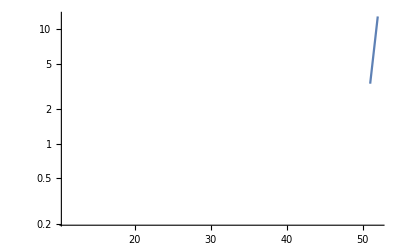

```mathematica
ListLogPlot[N[Eigenvalues[mat5Tree]+1]//Sort,PlotRange->All, Joined->True]
```

```mathematica
treeKeys6=Select[Keys[stubbornForm6],With[{g=stubbornForm6[#,"graph"]},TreeGraphQ[g]]&];Length[treeKeys6]
```

4513

```mathematica
Monitor[Table[MyPlanar[stubbornForm5,k],{k,treeKeys5}],k]//Tally
```

Tally::list: List expected at position 1 in Tally[$Aborted].

Tally[$Aborted]

```mathematica
MyPlanar[stubbornForm5,7738]
```

$Aborted

```mathematica
stubbornForm5[7738]
```

<|signature→7738,matrix→{{2,0,1,0,1},{0,2,1,2,1},{1,1,2,1,2},{0,2,1,2,1},{1,1,2,1,2}},graph→-Graphics-,vertexsets→{{1},{2,4},{3,5}},vertices→{1,2,3},edges→{{1,3},{2,3}},relations→{x7738==x29608+x51478,x7738==-x36898+x448,x7738==-x29888+x7458},links→{51478,29608},colortable→{{v124x35,v1x24x35},{0,v124x35+v1x24x35},{v124x35,v1x24x35},{0,v124x35+v1x24x35},{0,v124x35+v1x24x35},{v124x35+v1x24x35,0},{0,v124x35+v1x24x35},{0,v124x35+v1x24x35},{v124x35+v1x24x35,0},{0,v124x35+v1x24x35}},colofour→v124x35+v1x24x35,colortable2→{{v124x35,v1x24x35},{0,v124x35+v1x24x35},{v124x35,v1x24x35},{0,v124x35+v1x24x35},{0,v124x35+v1x24x35},{v124x35+v1x24x35,0},{0,v124x35+v1x24x35},{0,v124x35+v1x24x35},{v124x35+v1x24x35,0},{0,v124x35+v1x24x35}},comp→GreaterEqual,compwhy→No IH,marked→True,parents→{7704,7732,7576,7566,7458,7480,7306,6975,7003,6751,1143,1171,919,448},children→{{29608,51478}}|>